```mathematica
BlueC=RGBColor[0.2627,0.4313,1];
PurpleC=RGBColor[0.5411,0.0784,0.9607];
RedC=RGBColor[0.60,0.30,0];
```

# Energy divider coupling

1. The system has two TLSs coupled each to a thermal bath.
2. The energy levels of the two levels are significantly off-resonant (for example ω_L = 2 ω_R)
3. A three level system mediates the thermal flow between the off-resonant transitions.

## System Hamiltonians

Identity operator

```mathematica
Id[ve_,ho_]:=ve,ho
```

### Subsystem Hamiltonians

The system contains three subsystems L, M and R. L and R are two level systems. M is a three level system.

Combined form for the three non-interacting subsystem Hamiltonians

```mathematica
Subscript[Ĥ, sys]^0 = (ℏ Subscript[ω, L])/2 (|Subscript[e, L]><Subscript[e, L]|-|Subscript[g, L]><Subscript[g, L]|) + ℏ Subscript[ω, M](|Subscript[2, R]><Subscript[2, R]|-|Subscript[0, R]><Subscript[0, R]|) + (ℏ Subscript[ω, R])/2 (|Subscript[e, R]><Subscript[e, R]|-|Subscript[g, R]><Subscript[g, R]|)
```

```mathematica
HLSep[veL_,hoL_,veM_,hoM_,veR_,hoR_]:=({{(ℏ Subscript[ω, 1])/2, 0}, {0, -(ℏ Subscript[ω, 1])/2}})[[veL,hoL]]Id[veM,hoM]Id[veR,hoR]
```

```mathematica
HMSep[veL_,hoL_,veM_,hoM_,veR_,hoR_]:=Id[veL,hoL]({{ℏ Subscript[ω, 2], 0, 0}, {0, 0, 0}, {0, 0, -ℏ Subscript[ω, 2]}})[[veM,hoM]]Id[veR,hoR]
```

```mathematica
HRSep[veL_,hoL_,veM_,hoM_,veR_,hoR_]:=Id[veL,hoL]Id[veM,hoM]({{(ℏ Subscript[ω, 3])/2, 0}, {0, -(ℏ Subscript[ω, 3])/2}})[[veR,hoR]]
```

The twelve possible eigenstates are numbered as,
|1>	= |e,2,e>
|2>	= |e,2,g>
|3>	= |e,1,e>
|4>	= |e,1,g>
|5>	= |e,0,e>
|6>	= |e,0,g>
|7>	= |g,2,e>
|8>	= |g,2,g>
|9>	= |g,1,e>
|10>= |g,1,g>
|11>= |g,0,e>
|12>= |g,0,g>

Eigenstate mapping function, maps overall state (1 to 12) to subsystem L, M, R state,

```mathematica
EmapL[i_]:=(i,7+i,8+i,9+i,10+i,11+i,12)2+(i,1+i,2+i,3+i,4+i,5+i,6)1
EmapM[i_]:=(i,5+i,6+i,11+i,12)3+(i,3+i,4+i,9+i,10)2+(i,1+i,2+i,7+i,8)1
EmapR[i_]:=(i,2+i,4+i,6+i,8+i,10+i,12)2+(i,1+i,3+i,5+i,7+i,9+i,11)1
```

Matrix form of the three Hamiltonians

```mathematica
HL[ve_,ho_]:=HLSep[EmapL[ve],EmapL[ho],EmapM[ve],EmapM[ho],EmapR[ve],EmapR[ho]]
HM[ve_,ho_]:=HMSep[EmapL[ve],EmapL[ho],EmapM[ve],EmapM[ho],EmapR[ve],EmapR[ho]]
HR[ve_,ho_]:=HRSep[EmapL[ve],EmapL[ho],EmapM[ve],EmapM[ho],EmapR[ve],EmapR[ho]]
```

Non-interacting subsystem Hamiltonians as a matrix in the combined system space

```mathematica
Hsys0Matrix = Table[HL[ve,ho]+HM[ve,ho]+HR[ve,ho],{ve,1,12},{ho,1,12}];
MatrixForm[Hsys0Matrix]
```

((ℏ ω_1)/2+ℏ ω_2+(ℏ ω_3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (ℏ ω_1)/2+ℏ ω_2-(ℏ ω_3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (ℏ ω_1)/2+(ℏ ω_3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (ℏ ω_1)/2-(ℏ ω_3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (ℏ ω_1)/2-ℏ ω_2+(ℏ ω_3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (ℏ ω_1)/2-ℏ ω_2-(ℏ ω_3)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(ℏ ω_1)/2+ℏ ω_2+(ℏ ω_3)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ ω_1)/2+ℏ ω_2-(ℏ ω_3)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ ω_1)/2+(ℏ ω_3)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ ω_1)/2-(ℏ ω_3)/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ ω_1)/2-ℏ ω_2+(ℏ ω_3)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ ω_1)/2-ℏ ω_2-(ℏ ω_3)/2)

## Interaction Hamiltonian between the subsystems

The energy levels of the individual components are specially tuned in our model. 
	1. First of all, there are no direct interactions between L and R.
	2. The energy levels are prepared so that
		ω_L≃2 ω_M
		ω_R≃ω_M
	3. The interaction strengths between subsystems are given by γ_LM and γ_MR.

```mathematica
Subscript[Ĥ, sys]^1 = (ℏ Subscript[γ, LM])/2(|Subscript[g, L]><Subscript[e, L]|⊗|Subscript[2, M]><Subscript[0, M]| + |Subscript[e, L]><Subscript[g, L]|⊗|Subscript[0, M]><Subscript[2, M]|)⊗Subscript[I, R]
	+ (ℏ Subscript[γ, MR])/2 Subscript[I, L]⊗((|Subscript[1, M]><Subscript[0, M]|+|Subscript[2, M]><Subscript[1, M]|)⊗|Subscript[g, R]><Subscript[e, R]| + (|Subscript[0, M]><Subscript[1, M]|+|Subscript[1, M]><Subscript[2, M]|)⊗|Subscript[e, R]><Subscript[g, R]|)
```

Considering the above Hamiltonian, we write the interaction between L and M as,

```mathematica
HintLM[ve_,ho_]:=(ℏ γLM)/2 KroneckerProduct[KroneckerProduct[({{0, 0}, {1, 0}}),({{0, 0, 1}, {0, 0, 0}, {0, 0, 0}})]+KroneckerProduct[({{0, 1}, {0, 0}}),({{0, 0, 0}, {0, 0, 0}, {1, 0, 0}})],({{1, 0}, {0, 1}})][[ve,ho]]
```

Similarly, we write the interaction between M and R as,

```mathematica
HintMR[ve_,ho_]:=(ℏ γMR)/2 KroneckerProduct[({{1, 0}, {0, 1}}),KroneckerProduct[({{0, 1, 0}, {0, 0, 1}, {0, 0, 0}}),({{0, 0}, {1, 0}})]+KroneckerProduct[({{0, 0, 0}, {1, 0, 0}, {0, 1, 0}}),({{0, 1}, {0, 0}})]][[ve,ho]]
```

Interacting system Hamiltonian as a matrix in the combined system space

```mathematica
Hsys1Matrix = Table[HintLM[ve,ho]+HintMR[ve,ho],{ve,1,12},{ho,1,12}];
MatrixForm[Hsys1Matrix]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (γMR ℏ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (γMR ℏ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (γMR ℏ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (γMR ℏ)/2 | 0 | 0 | (γLM ℏ)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (γLM ℏ)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (γLM ℏ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (γLM ℏ)/2 | 0 | 0 | (γMR ℏ)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (γMR ℏ)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (γMR ℏ)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (γMR ℏ)/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Combined system Hamiltonian

```mathematica
Subscript[Ĥ, sys] = Subscript[Ĥ, sys]^0 + Subscript[Ĥ, sys]^1
```

```mathematica
HsysMatrix=Hsys0Matrix+Hsys1Matrix;
MatrixForm[HsysMatrix]
```

((ℏ ω_1)/2+ℏ ω_2+(ℏ ω_3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (ℏ ω_1)/2+ℏ ω_2-(ℏ ω_3)/2 | (γMR ℏ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (γMR ℏ)/2 | (ℏ ω_1)/2+(ℏ ω_3)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (ℏ ω_1)/2-(ℏ ω_3)/2 | (γMR ℏ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (γMR ℏ)/2 | (ℏ ω_1)/2-ℏ ω_2+(ℏ ω_3)/2 | 0 | (γLM ℏ)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (ℏ ω_1)/2-ℏ ω_2-(ℏ ω_3)/2 | 0 | (γLM ℏ)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (γLM ℏ)/2 | 0 | -(ℏ ω_1)/2+ℏ ω_2+(ℏ ω_3)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (γLM ℏ)/2 | 0 | -(ℏ ω_1)/2+ℏ ω_2-(ℏ ω_3)/2 | (γMR ℏ)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (γMR ℏ)/2 | -(ℏ ω_1)/2+(ℏ ω_3)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ ω_1)/2-(ℏ ω_3)/2 | (γMR ℏ)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (γMR ℏ)/2 | -(ℏ ω_1)/2-ℏ ω_2+(ℏ ω_3)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ℏ ω_1)/2-ℏ ω_2-(ℏ ω_3)/2)

### Visualize the energy levels of the combined system

```mathematica
unitassum={ℏ->1};
```

#### Bare energy levels without the interaction Hamiltonian

Function for shifting the eigenvalues from Mathematica to our representation

```mathematica
Shift1[i_]:=i,1 12+i,2 6+i,3 8+i,4 2+i,5 10+i,6 4+i,7 11+i,8 5+i,9 7+i,10 1+i,11 9+i,12 3
```

```mathematica
Hsys0EVal[i_]:=Eigenvalues[Hsys0Matrix][[Shift1[i]]]
Hsys0EVec[i_]:=Eigenvectors[Hsys0Matrix][[Shift1[i]]]

Table[{Hsys0EVal[i],MatrixForm[Hsys0EVec[i]]},{i,1,12}]
```

{{1/2 ℏ (ω_1+2 ω_2+ω_3),(1
0
0
0
0
0
0
0
0
0
0
0)},{1/2 ℏ (ω_1+2 ω_2-ω_3),(0
1
0
0
0
0
0
0
0
0
0
0)},{1/2 ℏ (ω_1+ω_3),(0
0
1
0
0
0
0
0
0
0
0
0)},{1/2 ℏ (ω_1-ω_3),(0
0
0
1
0
0
0
0
0
0
0
0)},{1/2 ℏ (ω_1-2 ω_2+ω_3),(0
0
0
0
1
0
0
0
0
0
0
0)},{1/2 ℏ (ω_1-2 ω_2-ω_3),(0
0
0
0
0
1
0
0
0
0
0
0)},{1/2 ℏ (-ω_1+2 ω_2+ω_3),(0
0
0
0
0
0
1
0
0
0
0
0)},{1/2 ℏ (-ω_1+2 ω_2-ω_3),(0
0
0
0
0
0
0
1
0
0
0
0)},{1/2 ℏ (-ω_1+ω_3),(0
0
0
0
0
0
0
0
1
0
0
0)},{1/2 ℏ (-ω_1-ω_3),(0
0
0
0
0
0
0
0
0
1
0
0)},{1/2 ℏ (-ω_1-2 ω_2+ω_3),(0
0
0
0
0
0
0
0
0
0
1
0)},{1/2 ℏ (-ω_1-2 ω_2-ω_3),(0
0
0
0
0
0
0
0
0
0
0
1)}}

#### Dressed energy levels with the interaction Hamiltonian

Function for shifting the eigenvalues from Mathematica to our representation

```mathematica
Shift2[i_]:=i,1 8+i,2 12+i,3 10+i,4 2+i,5 1+i,6 4+i,7 3+i,8 6+i,9 5+i,10 11+i,11 9+i,12 7
```

```mathematica
HsysEVal[i_]:=Eigenvalues[HsysMatrix][[Shift2[i]]]
HsysEVec[i_]:=Eigenvectors[HsysMatrix][[Shift2[i]]]
```

#### Comparison of bare and dressed energy levels

```mathematica
Manipulate[Module[{temp1,temp2},
temp1=Table[Hsys0EVal[i],{i,1,12}]/.Flatten[{Subscript[ω, 1]->ωL,Subscript[ω, 2]->ωM,Subscript[ω, 3]->ωR,unitassum}];
temp2=Table[HsysEVal[i],{i,1,12}]/.Flatten[{Subscript[ω, 1]->ωL,Subscript[ω, 2]->ωM,Subscript[ω, 3]->ωR,γLM->γLMs,γMR->γMRs,unitassum}];
{
Plot[temp1,{t,0,2},
PlotLegends->{
"|1_BARE> = |e2e>","|2_BARE> = |e2g>","|3_BARE> = |e1e>","|4_BARE> = |e1g>",
"|5_BARE> = |e0e>","|6_BARE> = |e0g>","|7_BARE> = |g2e>","|8_BARE> = |g2g>",
"|9_BARE> = |g1e>","|10_BARE> = |g1g>","|11_BARE> = |g0e>","|12_BARE> = |g0g>"},
AxesLabel->{None,"Energy"},PlotRange->{-3,3},Ticks->{None,Automatic},ImageSize->Large],
Plot[temp2,{t,0,2},
PlotLegends->{
"|1_DRE> = |e2e>","|2_DRE>","|3_DRE>","|4_DRE>",
"|5_DRE>","|6_DRE>","|7_DRE>","|8_DRE>",
"|9_DRE>","|10_DRE>","|11_DRE>","|12_DRE> = |g0g>"},
AxesLabel->{None,"Energy"},PlotRange->{-3,3},Ticks->{None,Automatic},ImageSize->Large]
}],
Delimiter,Item["Frequencies",Alignment->Center],
{{ωL,2.1},0,3},
{{ωM,1},0,3},
{{ωR,0.9},0,3},
Delimiter,Item["Interactions",Alignment->Center],
{{γLMs,0.01},0,0.3},
{{γMRs,0.01},0,0.3}]
```

The interaction Hamiltonian is in the weak regime, hence the energy levels are mostly unchanged by the interaction Hamiltonian.

## Density Matrix

In the combined system, the density matrix is 12×12.

```mathematica
ρMatrix[t_]:=Table[Subscript[ρ, ve,ho][t],{ve,1,12},{ho,1,12}]
```

```mathematica
MatrixForm[ρMatrix[t]]
```

(ρ_(1,1)[t] | ρ_(1,2)[t] | ρ_(1,3)[t] | ρ_(1,4)[t] | ρ_(1,5)[t] | ρ_(1,6)[t] | ρ_(1,7)[t] | ρ_(1,8)[t] | ρ_(1,9)[t] | ρ_(1,10)[t] | ρ_(1,11)[t] | ρ_(1,12)[t]
ρ_(2,1)[t] | ρ_(2,2)[t] | ρ_(2,3)[t] | ρ_(2,4)[t] | ρ_(2,5)[t] | ρ_(2,6)[t] | ρ_(2,7)[t] | ρ_(2,8)[t] | ρ_(2,9)[t] | ρ_(2,10)[t] | ρ_(2,11)[t] | ρ_(2,12)[t]
ρ_(3,1)[t] | ρ_(3,2)[t] | ρ_(3,3)[t] | ρ_(3,4)[t] | ρ_(3,5)[t] | ρ_(3,6)[t] | ρ_(3,7)[t] | ρ_(3,8)[t] | ρ_(3,9)[t] | ρ_(3,10)[t] | ρ_(3,11)[t] | ρ_(3,12)[t]
ρ_(4,1)[t] | ρ_(4,2)[t] | ρ_(4,3)[t] | ρ_(4,4)[t] | ρ_(4,5)[t] | ρ_(4,6)[t] | ρ_(4,7)[t] | ρ_(4,8)[t] | ρ_(4,9)[t] | ρ_(4,10)[t] | ρ_(4,11)[t] | ρ_(4,12)[t]
ρ_(5,1)[t] | ρ_(5,2)[t] | ρ_(5,3)[t] | ρ_(5,4)[t] | ρ_(5,5)[t] | ρ_(5,6)[t] | ρ_(5,7)[t] | ρ_(5,8)[t] | ρ_(5,9)[t] | ρ_(5,10)[t] | ρ_(5,11)[t] | ρ_(5,12)[t]
ρ_(6,1)[t] | ρ_(6,2)[t] | ρ_(6,3)[t] | ρ_(6,4)[t] | ρ_(6,5)[t] | ρ_(6,6)[t] | ρ_(6,7)[t] | ρ_(6,8)[t] | ρ_(6,9)[t] | ρ_(6,10)[t] | ρ_(6,11)[t] | ρ_(6,12)[t]
ρ_(7,1)[t] | ρ_(7,2)[t] | ρ_(7,3)[t] | ρ_(7,4)[t] | ρ_(7,5)[t] | ρ_(7,6)[t] | ρ_(7,7)[t] | ρ_(7,8)[t] | ρ_(7,9)[t] | ρ_(7,10)[t] | ρ_(7,11)[t] | ρ_(7,12)[t]
ρ_(8,1)[t] | ρ_(8,2)[t] | ρ_(8,3)[t] | ρ_(8,4)[t] | ρ_(8,5)[t] | ρ_(8,6)[t] | ρ_(8,7)[t] | ρ_(8,8)[t] | ρ_(8,9)[t] | ρ_(8,10)[t] | ρ_(8,11)[t] | ρ_(8,12)[t]
ρ_(9,1)[t] | ρ_(9,2)[t] | ρ_(9,3)[t] | ρ_(9,4)[t] | ρ_(9,5)[t] | ρ_(9,6)[t] | ρ_(9,7)[t] | ρ_(9,8)[t] | ρ_(9,9)[t] | ρ_(9,10)[t] | ρ_(9,11)[t] | ρ_(9,12)[t]
ρ_(10,1)[t] | ρ_(10,2)[t] | ρ_(10,3)[t] | ρ_(10,4)[t] | ρ_(10,5)[t] | ρ_(10,6)[t] | ρ_(10,7)[t] | ρ_(10,8)[t] | ρ_(10,9)[t] | ρ_(10,10)[t] | ρ_(10,11)[t] | ρ_(10,12)[t]
ρ_(11,1)[t] | ρ_(11,2)[t] | ρ_(11,3)[t] | ρ_(11,4)[t] | ρ_(11,5)[t] | ρ_(11,6)[t] | ρ_(11,7)[t] | ρ_(11,8)[t] | ρ_(11,9)[t] | ρ_(11,10)[t] | ρ_(11,11)[t] | ρ_(11,12)[t]
ρ_(12,1)[t] | ρ_(12,2)[t] | ρ_(12,3)[t] | ρ_(12,4)[t] | ρ_(12,5)[t] | ρ_(12,6)[t] | ρ_(12,7)[t] | ρ_(12,8)[t] | ρ_(12,9)[t] | ρ_(12,10)[t] | ρ_(12,11)[t] | ρ_(12,12)[t])

## Thermal interactions with the baths

The two corner two-level systems interact thermally with respective bosonic thermal baths B_L and B_R with temperatures T_L and T_R.

```mathematica
Subscript[Ĥ, bath]^P = ℏ ∑_k Subscript[ω, k] Subscript[â, k]^P†Subscript[â, k]^P
```

Interaction Hamiltonian between the thermal bath L or R with the two TLSs is modelled after the Spin-Boson model in the x-component

```mathematica
Subscript[Ĥ, sys-bath]^P = ℏ Subscript[σ, X]^P∑_k Subscript[g, k](Subscript[â, k]^P+Subscript[â, k]^P†)
```

Note - Here, P = L, R (or in the simulations P = 1, 3)

## Pauli matrices

### In z-base representation

|+z>=(1,0)
|-z>=(0,1)

```mathematica
Subscript[σ, axis_][ve_,ho_]:=axis,1({{0, 1}, {1, 0}})[[ve,ho]]+axis,2({{0, -ⅈ}, {ⅈ, 0}})[[ve,ho]]+axis,3({{1, 0}, {0, -1}})[[ve,ho]];
```

```mathematica
{Table[Subscript[σ, 1][ve,ho],{ve,1,2},{ho,1,2}],Table[Subscript[σ, 2][ve,ho],{ve,1,2},{ho,1,2}],Table[Subscript[σ, 3][ve,ho],{ve,1,2},{ho,1,2}]};
Map[MatrixForm,%,1]
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

### In compound system representation

```mathematica
Subscript[σ, P_,axis_][ve_,ho_]:=
P,1(Subscript[σ, axis][EmapL[ve],EmapL[ho]]Id[EmapM[ve],EmapM[ho]]Id[EmapR[ve],EmapR[ho]])+
P,2(Id[EmapL[ve],EmapL[ho]]Id [EmapM[ve],EmapM[ho]]Subscript[σ, axis][EmapR[ve],EmapR[ho]])

Subscript[σMatrix, P_,axis_]:=Table[Subscript[σ, P,axis][ve,ho],{ve,1,12},{ho,1,12}]
Subscript[σPMatrix, P_]:=1/2(Subscript[σMatrix, P,1]+ⅈ Subscript[σMatrix, P,2])
Subscript[σMMatrix, P_]:=1/2(Subscript[σMatrix, P,1]-ⅈ Subscript[σMatrix, P,2])
```

```mathematica
{MatrixForm[Subscript[σMatrix, 1,1]],MatrixForm[Subscript[σMatrix, 2,1]]}
```

{(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

## System-bath interactions

The two two-level systems interact thermally with respective bosonic thermal baths B_L and B_R with temperatures T_L and T_R.

```mathematica
Subscript[Ĥ, bath]^P = ℏ ∑_k Subscript[ω, k] Subscript[â, k]^P†Subscript[â, k]^P
```

Interaction Hamiltonian between the thermal bath L or R with the two TLSs is modelled after the Spin-Boson model in the x-component

```mathematica
Subscript[H, TLS-bath]^P=ℏ Subscript[σ, X]^P∑_k Subscript[g, k](Subscript[a, k]^P+Subscript[a, k]^P†)
```

To get the Lindbladian operators, we use equation (15) of Optically Controlled Quantum Thermal Gate paper.

The inter-TLS interaction Hamiltonian is supposed to be in the weak regime. The energy eigensystem is minimally affected by the interaction.
This means that it is enough to model the thermal interactions in the bare eigensystem of only the individual TLS Hamiltonians.

```mathematica
Table[{Hsys0EVal[i],MatrixForm[Hsys0EVec[i]]},{i,1,12}]
```

{{1/2 ℏ (ω_1+2 ω_2+ω_3),(1
0
0
0
0
0
0
0
0
0
0
0)},{1/2 ℏ (ω_1+2 ω_2-ω_3),(0
1
0
0
0
0
0
0
0
0
0
0)},{1/2 ℏ (ω_1+ω_3),(0
0
1
0
0
0
0
0
0
0
0
0)},{1/2 ℏ (ω_1-ω_3),(0
0
0
1
0
0
0
0
0
0
0
0)},{1/2 ℏ (ω_1-2 ω_2+ω_3),(0
0
0
0
1
0
0
0
0
0
0
0)},{1/2 ℏ (ω_1-2 ω_2-ω_3),(0
0
0
0
0
1
0
0
0
0
0
0)},{1/2 ℏ (-ω_1+2 ω_2+ω_3),(0
0
0
0
0
0
1
0
0
0
0
0)},{1/2 ℏ (-ω_1+2 ω_2-ω_3),(0
0
0
0
0
0
0
1
0
0
0
0)},{1/2 ℏ (-ω_1+ω_3),(0
0
0
0
0
0
0
0
1
0
0
0)},{1/2 ℏ (-ω_1-ω_3),(0
0
0
0
0
0
0
0
0
1
0
0)},{1/2 ℏ (-ω_1-2 ω_2+ω_3),(0
0
0
0
0
0
0
0
0
0
1
0)},{1/2 ℏ (-ω_1-2 ω_2-ω_3),(0
0
0
0
0
0
0
0
0
0
0
1)}}

## Calculating positive transition frequencies

We work under assumption that energy levels are minimally affected by the interaction term γ.

Assumptions on energy levels

```mathematica
ωassum={Subscript[ω, 1]->2,Subscript[ω, 2]->0.61,Subscript[ω, 3]->0.1,γLM->0.02,γMR->0.03};
```

Transition frequencies,

```mathematica
ω[m_,n_]:=Simplify[(Hsys0EVal[m]-Hsys0EVal[n])/ℏ]
```

Unique and positive transition frequencies,

```mathematica
ω[i_]:=ω[i]=Module[{temp1,temp2,temp3},
temp1=Flatten[Table[ω[m,n],{m,1,12},{n,m+1,12}]];
temp2=temp1/.ωassum;
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp1 temp3,0][[i]]
]
ωsize:=Module[{temp1,temp2,temp3},
temp1=Flatten[Table[ω[m,n],{m,1,12},{n,m+1,12}]];
temp2=temp1/.ωassum;
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
Dimensions[DeleteCases[temp1 temp3,0]][[1]]
]
ωplus[i_]:=Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[Table[HsysEVal[m],{m,1,12},{n,m+1,12}]];
temp1=Flatten[Table[ω[m,n],{m,1,12},{n,m+1,12}]];
temp2=temp1/.ωassum;
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp0 temp3,0][[i]]
]
ωminus[i_]:=Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[Table[HsysEVal[m],{m,1,12},{n,m+1,12}]];
temp1=Flatten[Table[ω[m,n],{m,1,12},{n,m+1,12}]];
temp2=temp1/.ωassum;
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp0 temp3,0][[i]]
]
```

```mathematica
Table[ω[i],{i,1,ωsize}]
ωsize
```

{ω_3,ω_2,ω_2+ω_3,2 ω_2,2 ω_2+ω_3,ω_1,ω_1+ω_3,ω_1+ω_2,ω_1+ω_2+ω_3,ω_1+2 ω_2,ω_1+2 ω_2+ω_3,ω_2-ω_3,2 ω_2-ω_3,ω_1-ω_3,ω_1+ω_2-ω_3,ω_1+2 ω_2-ω_3,ω_1-ω_2,ω_1-ω_2+ω_3,ω_1-ω_2-ω_3,ω_1-2 ω_2,ω_1-2 ω_2+ω_3,ω_1-2 ω_2-ω_3}

22

## Modelling thermal interactions

### Get projection matrices Π(ϵ)

Assume the energy levels are such that all eigenvalues are non-degenerate. The projection matrix then reads,

```mathematica
Π̂[Subscript[ϵ, i]] = |i><i|
```

where ϵ_i is the energy of the i^th state (in the bare basis).

In the bare basis, ϵ_i for a known state |i> is given by

```mathematica
|i> = |Subscript[i, L]>⊗|Subscript[i, M]>⊗|Subscript[i, R]>

Subscript[ϵ, i] = Subscript[E, L][Subscript[i, L]]+Subscript[E, M][Subscript[i, M]]+Subscript[E, R][Subscript[i, R]]
```

```mathematica
πMatrix[i_]:=Table[i,j i,k,{j,1,12},{k,1,12}]
```

### Get Lindblad operators A^P(ω)

From Eq. (15) of Optically Controlled Quantum Thermal Gate, we see that, for the above (Ĥ)_(sys-bath)^P interaction Hamiltonian, the Lindblad operators are given by,

```mathematica
Subscript[Â, P][ω] = ∑_(ϵ1-ϵ2=ℏ ω) Π̂[ϵ2].(Subscript[σ̂, x]^P).Π̂[ϵ1]
	  = ∑_(i=1)^N ∑_(j=1)^N ℏ ω,Subscript[ϵ, i]-Subscript[ϵ, j]Π̂[Subscript[ϵ, j]].(Subscript[σ̂, x]^P).Π̂[Subscript[ϵ, i]]
	  = ∑_(i=1)^N ∑_(j=1)^N ℏ ω,Subscript[ϵ, i]-Subscript[ϵ, j]|j><j|.(Subscript[σ̂, x]^P).|i><i|
	  = ∑_(i=1)^N ∑_(j=1)^N ℏ ω,Subscript[ϵ, i]-Subscript[ϵ, j]<j|Subscript[σ̂, x]^P|i> |j><i|
```

WLOG Consider the matrix element of (σ̂)_x^1,

```mathematica
<j|Subscript[σ̂, x]^1|i> = (<Subscript[j, L]|⊗<Subscript[j, M]|⊗<Subscript[j, R]|)(Subscript[σ̂, x]^L ⊗ I ⊗ I)(|Subscript[i, L]>⊗|Subscript[i, M]>⊗|Subscript[i, R]>)
		  = <Subscript[j, L]|Subscript[σ̂, x]^L|Subscript[i, L]> <Subscript[j, M]|Subscript[i, M]> <Subscript[j, R]|Subscript[i, R]>
		  = If[Subscript[j, L]≠Subscript[i, L],1,0] Subscript[j, M],Subscript[i, M]Subscript[j, R],Subscript[i, R]
```

For the If function to be non-zero, the states of the subsystem L have to be different.
For the Kronecker deltas to be non-zero, the states of ‘other subsystems’ M and R have to be equal.

```mathematica
Subscript[Â, 1][ω] = ∑_(i=1)^N ∑_(j=1)^N ℏ ω,Subscript[ϵ, i]-Subscript[ϵ, j]<j|Subscript[σ̂, x]^1|i> |j><i|
		=∑_(Subscript[i, L],Subscript[i, M],Subscript[i, R]) ∑_(Subscript[j, L],Subscript[j, M],Subscript[j, R]) ℏ ω,Subscript[ϵ, i]-Subscript[ϵ, j]If[Subscript[j, L]≠Subscript[i, L],1,0] Subscript[j, M],Subscript[i, M]Subscript[j, R],Subscript[i, R] |j><i|
		=∑_(Subscript[i, L],Subscript[i, M],Subscript[i, R]) ∑_Subscript[j, L] ℏ ω,Subscript[ϵ, i]-Subscript[ϵ, j]If[Subscript[j, L]≠Subscript[i, L],1,0] |j><i|
```

Now consider ℏ ω = ϵ_i-ϵ_j, under condition that M and R in i and j have the same state,

```mathematica
ℏ ω = Subscript[ϵ, i]-Subscript[ϵ, j] = (Subscript[E, L][Subscript[i, L]]+Subscript[E, M][Subscript[i, M]]+Subscript[E, R][Subscript[i, R]])-(Subscript[E, L][Subscript[j, L]]+Subscript[E, M][Subscript[j, M]]+Subscript[E, R][Subscript[j, R]]) = Subscript[E, L][Subscript[i, L]]-Subscript[E, R][Subscript[j, L]]
```

Since ω is positive, that means i_L has to be the excited state, and j_L has to be the ground state. For this, we get the simplified form

```mathematica
ℏ ω = Subscript[E, L][Subscript[i, L]]-Subscript[E, R][Subscript[j, L]] = ℏ Subscript[ω, 1]

<j|Subscript[σ̂, x]^1|i> = If[Subscript[j, L]≠Subscript[i, L],1,0] Subscript[j, M],Subscript[i, M]Subscript[j, R],Subscript[i, R] = 1
		  
|j><i| = (|Subscript[j, L]>⊗|Subscript[j, M]>⊗|Subscript[j, R]>)(<Subscript[i, L]|⊗<Subscript[i, M]|⊗<Subscript[i, R]|)
		 = |Subscript[j, L]><Subscript[i, L]|⊗|Subscript[i, M]><Subscript[i, M]|⊗|Subscript[i, R]><Subscript[i, R]|
		  = SubMinus[Ŝ]⊗|Subscript[i, M]><Subscript[i, M]|⊗|Subscript[i, R]><Subscript[i, R]|
```

Now carry out the summation over i_L and j_L, with i_L=e and j_L=g being the only non-zero term

```mathematica
Subscript[Â, 1][ω] =∑_(Subscript[i, L],Subscript[i, M],Subscript[i, R]) ∑_Subscript[j, L] ℏ ω,Subscript[ϵ, i]-Subscript[ϵ, j]If[Subscript[j, L]≠Subscript[i, L],1,0] |j><i|
		= ∑_(Subscript[i, M],Subscript[i, R]) ℏ ω,ℏ Subscript[ω, 1](SubMinus[Ŝ]⊗|Subscript[i, M]><Subscript[i, M]|⊗|Subscript[i, R]><Subscript[i, R]|)
		= ℏ ω,ℏ Subscript[ω, 1](SubMinus[Ŝ]⊗I⊗I)
		= ω,Subscript[ω, 1](SubMinus[Ŝ]⊗I⊗I)
```

Therefore, for ω>0 we have, assuming that the energy levels are NOT specifically DESIGNED to be difficult/pathological (see the bunch of inequalities in the code below)

```mathematica
Subscript[Â, 1][ω] = ω,Subscript[ω, 1](SubMinus[Ŝ]⊗I⊗I)
Subscript[Â, 2][ω] = ω,Subscript[ω, 3](I⊗I⊗SubMinus[Ŝ])
```

Method 1 - Use some practical values that remove the pathological cases

```mathematica
OneMatrix[ve_,ho_,N_]:=Table[ve,i ho,j,{i,1,N},{j,1,N}]
```

```mathematica
Subscript[AMatrix, P_][ωs_]:=Simplify[∑_(i=1)^12 ∑_(j=1)^12 ωs,ω[i,j](Subscript[σMatrix, P,1][[j,i]]OneMatrix[j,i,12]),Assumptions->{Subscript[ω, 1]==10,Subscript[ω, 2]==1,Subscript[ω, 3]==0.1}]
```

Method 2 - List all the pathological cases

```mathematica
Subscript[AMatrix, P_][ωs_]:=Simplify[∑_(i=1)^12 ∑_(j=1)^12 ωs,ω[i,j](Subscript[σMatrix, P,1][[j,i]]OneMatrix[j,i,12]),Assumptions->{
Subscript[ω, 1]>0,Subscript[ω, 2]>0,Subscript[ω, 3]>0,Subscript[ω, 1]≠Subscript[ω, 2],Subscript[ω, 1]≠Subscript[ω, 3],Subscript[ω, 2]≠Subscript[ω, 3],
Subscript[ω, 1]≠2 Subscript[ω, 2],Subscript[ω, 1]≠2 Subscript[ω, 3],Subscript[ω, 2]≠2 Subscript[ω, 3],Subscript[ω, 2]≠2 Subscript[ω, 1],Subscript[ω, 3]≠2 Subscript[ω, 1],Subscript[ω, 3]≠2 Subscript[ω, 2],
Subscript[ω, 1]≠Subscript[ω, 2]+Subscript[ω, 3],Subscript[ω, 2]≠Subscript[ω, 1]+Subscript[ω, 3],Subscript[ω, 3]≠Subscript[ω, 1]+Subscript[ω, 2],

2 Subscript[ω, 1]≠Subscript[ω, 2]+Subscript[ω, 3],2 Subscript[ω, 1]≠Subscript[ω, 3]-Subscript[ω, 2],2 Subscript[ω, 1]≠Subscript[ω, 2]-Subscript[ω, 3],
2 Subscript[ω, 2]≠Subscript[ω, 3]+Subscript[ω, 1],2 Subscript[ω, 2]≠Subscript[ω, 1]-Subscript[ω, 3],2 Subscript[ω, 2]≠Subscript[ω, 3]-Subscript[ω, 1],
2 Subscript[ω, 3]≠Subscript[ω, 1]+Subscript[ω, 2],2 Subscript[ω, 3]≠Subscript[ω, 2]-Subscript[ω, 1],2 Subscript[ω, 3]≠Subscript[ω, 1]-Subscript[ω, 2],

Subscript[ω, 3]≠2(Subscript[ω, 1]+Subscript[ω, 2]),Subscript[ω, 3]≠2 (Subscript[ω, 1]-Subscript[ω, 2]),Subscript[ω, 3]≠2 (Subscript[ω, 2]-Subscript[ω, 1]),
Subscript[ω, 1]≠2(Subscript[ω, 2]+Subscript[ω, 3]),Subscript[ω, 1]≠2(Subscript[ω, 2]- Subscript[ω, 3]),Subscript[ω, 1]≠2(Subscript[ω, 3]- Subscript[ω, 2])
}]
```

Lindbladian terms involve a summation of A^P(ω) terms for positive omega, and most turn out to be zero.

```mathematica
Table[MatrixForm[Subscript[AMatrix, P][ω[i]]],{P,1,2},{i,1,ωsize}]//MatrixForm
```

((0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0))

Pre-calculated matrices under uniqueness assumption,

```mathematica
temp=({{({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}})}, {({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}), ({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}})}});
Subscript[AMatrixω, P_][i_]:=temp[[P,i]]
```

Non-zero Lindblad operators correspond to the frequencies,

```mathematica
ω[6]
ω[1]
```

ω_1

ω_3

### Calculate Lindbladian terms

Linbladian for the Markovian quantum master equation, as given in Eq. (13) of Optically Controlled Quantum Thermal Gate

```mathematica
Subscript[ℒ̂, P][ρ̂] = ∑_(ω>0) (Subscript[𝒥, P][ω](1+Subscript[n, P][ω])(Subscript[Â, P][ω] ρ̂ Subscript[Â, P][ω]†-1/2{Subscript[Â, P][ω]†Subscript[Â, P][ω],ρ̂}) + Subscript[𝒥, P][ω] Subscript[n, P][ω](Subscript[Â, P][ω]†ρ̂ Subscript[Â, P][ω]-1/2{Subscript[Â, P][ω]Subscript[Â, P][ω]†,ρ̂}))
Subscript[Â, P][ω] = ∑_(ϵ1-ϵ2=ℏ ω) Π̂[ϵ2].(Subscript[σ̂, x]^P).Π̂[ϵ1]
	  = ∑_(i=1)^N ∑_(j=1)^N ℏ ω,Subscript[ϵ, i]-Subscript[ϵ, j]Π̂[Subscript[ϵ, j]].(Subscript[σ̂, x]^P).Π̂[Subscript[ϵ, i]]
```

```mathematica
Subscript[LinMatrix, P_][ρ_]:=Subscript[LinMatrix, P][ρ]=Simplify[∑_(i=1)^ωsize (Subscript[J, P][ω[i]](1+Subscript[NBE, P][ω[i]])(Subscript[AMatrixω, P][i].ρ.Subscript[AMatrixω, P][i]†-1/2(Subscript[AMatrixω, P][i]†.Subscript[AMatrixω, P][i].ρ+ρ.Subscript[AMatrixω, P][i]†.Subscript[AMatrixω, P][i]))+Subscript[J, P][ω[i]]Subscript[NBE, P][ω[i]](Subscript[AMatrixω, P][i]†.ρ.Subscript[AMatrixω, P][i]-1/2(Subscript[AMatrixω, P][i].Subscript[AMatrixω, P][i]†.ρ+ρ.Subscript[AMatrixω, P][i].Subscript[AMatrixω, P][i]†)))]
```

Net thermal decaying rate Τ_P[i,j] from state | i > to state | j > while releasing energy to reservoir P. Note i > j.
Τs_P[i,j] is used due to variable naming issues.

```mathematica
Subscript[Γ, i,j]^P = Subscript[𝒥, P][Subscript[ω, i,j]]((1+Subscript[n, P][Subscript[ω, i,j]])Subscript[ρ, i,i][t]-Subscript[n, P][Subscript[ω, i,j]]Subscript[ρ, j,j][t])
```

```mathematica
Subscript[Τs, P_][i_,j_]:=Subscript[J, P][ω[i,j]](1+Subscript[NBE, P][ω[i,j]])Subscript[ρ, i,i][t]-Subscript[J, P][ω[i,j]]Subscript[NBE, P][ω[i,j]]Subscript[ρ, j,j][t]
```

Mathematica function for arithmetically proper replacements,

```mathematica
ReplaceArithmetically[expr_,orig_,repl_]:=
Module[{f},
(*Actual replacement function, but it is not Listable*)
f[exprs_,origs_,repls_]:=Module[{q,r},
{q,r}=PolynomialReduce[exprs,origs,{}];
q.repls+r
];
(*Construct for making the function Listable in only the first argument*)
Function[t,f[t,orig,repl],{Listable}][expr]
]
```

```mathematica
ReplaceArithmetically[Subscript[LinMatrix, 1][ρMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,12},{j,1,12}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,12},{j,1,12}]]
];
Collect[Expand[%],Flatten[Table[Subscript[ρ, i,j][t],{i,1,12},{j,1,12}]],Simplify];
MatrixForm[%]
ReplaceArithmetically[Subscript[LinMatrix, 2][ρMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,12},{j,1,12}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,12},{j,1,12}]]
];
Collect[Expand[%],Flatten[Table[Subscript[ρ, i,j][t],{i,1,12},{j,1,12}]],Simplify];
MatrixForm[%]
```

(-Τ_1[1,7] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,2)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(7,8)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,3)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(7,9)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,4)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(7,10)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,5)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(7,11)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,6)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(7,12)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(1,7)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(1,8)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(1,9)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(1,10)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(1,11)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(1,12)[t]
-J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,1)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(8,7)[t] | -Τ_1[2,8] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,3)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(8,9)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,4)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(8,10)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,5)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(8,11)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,6)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(8,12)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(2,7)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(2,8)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(2,9)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(2,10)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(2,11)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(2,12)[t]
-J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,1)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(9,7)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,2)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(9,8)[t] | -Τ_1[3,9] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,4)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(9,10)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,5)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(9,11)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,6)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(9,12)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(3,7)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(3,8)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(3,9)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(3,10)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(3,11)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(3,12)[t]
-J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,1)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(10,7)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,2)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(10,8)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,3)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(10,9)[t] | -Τ_1[4,10] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,5)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(10,11)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,6)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(10,12)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(4,7)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(4,8)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(4,9)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(4,10)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(4,11)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(4,12)[t]
-J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,1)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(11,7)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,2)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(11,8)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,3)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(11,9)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,4)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(11,10)[t] | -Τ_1[5,11] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,6)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(11,12)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(5,7)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(5,8)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(5,9)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(5,10)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(5,11)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(5,12)[t]
-J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,1)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(12,7)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,2)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(12,8)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,3)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(12,9)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,4)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(12,10)[t] | -J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,5)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(12,11)[t] | -Τ_1[6,12] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(6,7)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(6,8)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(6,9)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(6,10)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(6,11)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(6,12)[t]
-1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(7,1)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(7,2)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(7,3)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(7,4)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(7,5)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(7,6)[t] | Τ_1[1,7] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,2)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(7,8)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,3)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(7,9)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,4)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(7,10)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,5)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(7,11)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,6)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(7,12)[t]
-1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(8,1)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(8,2)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(8,3)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(8,4)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(8,5)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(8,6)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,1)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(8,7)[t] | Τ_1[2,8] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,3)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(8,9)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,4)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(8,10)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,5)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(8,11)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,6)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(8,12)[t]
-1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(9,1)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(9,2)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(9,3)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(9,4)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(9,5)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(9,6)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,1)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(9,7)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,2)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(9,8)[t] | Τ_1[3,9] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,4)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(9,10)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,5)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(9,11)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,6)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(9,12)[t]
-1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(10,1)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(10,2)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(10,3)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(10,4)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(10,5)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(10,6)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,1)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(10,7)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,2)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(10,8)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,3)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(10,9)[t] | Τ_1[4,10] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,5)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(10,11)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,6)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(10,12)[t]
-1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(11,1)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(11,2)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(11,3)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(11,4)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(11,5)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(11,6)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,1)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(11,7)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,2)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(11,8)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,3)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(11,9)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,4)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(11,10)[t] | Τ_1[5,11] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,6)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(11,12)[t]
-1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(12,1)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(12,2)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(12,3)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(12,4)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(12,5)[t] | -1/2 J_1[ω_1] (1+2 NBE_1[ω_1]) ρ_(12,6)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,1)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(12,7)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,2)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(12,8)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,3)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(12,9)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,4)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(12,10)[t] | J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,5)[t]-J_1[ω_1] NBE_1[ω_1] ρ_(12,11)[t] | Τ_1[6,12])

(-Τ_2[1,2] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(1,2)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(1,3)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(2,4)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(1,4)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(1,5)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(2,6)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(1,6)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(1,7)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(2,8)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(1,8)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(1,9)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(2,10)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(1,10)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(1,11)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(2,12)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(1,12)[t]
-1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(2,1)[t] | Τ_2[1,2] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(2,3)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(1,3)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(2,4)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(2,5)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(1,5)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(2,6)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(2,7)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(1,7)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(2,8)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(2,9)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(1,9)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(2,10)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(2,11)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(1,11)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(2,12)[t]
-J_2[ω_3] (1+NBE_2[ω_3]) ρ_(3,1)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(4,2)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(3,2)[t] | -Τ_2[3,4] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(3,4)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(3,5)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(4,6)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(3,6)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(3,7)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(4,8)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(3,8)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(3,9)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(4,10)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(3,10)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(3,11)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(4,12)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(3,12)[t]
-1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(4,1)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(3,1)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(4,2)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(4,3)[t] | Τ_2[3,4] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(4,5)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(3,5)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(4,6)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(4,7)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(3,7)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(4,8)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(4,9)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(3,9)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(4,10)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(4,11)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(3,11)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(4,12)[t]
-J_2[ω_3] (1+NBE_2[ω_3]) ρ_(5,1)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(6,2)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(5,2)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(5,3)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(6,4)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(5,4)[t] | -Τ_2[5,6] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(5,6)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(5,7)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(6,8)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(5,8)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(5,9)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(6,10)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(5,10)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(5,11)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(6,12)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(5,12)[t]
-1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(6,1)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(5,1)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(6,2)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(6,3)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(5,3)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(6,4)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(6,5)[t] | Τ_2[5,6] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(6,7)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(5,7)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(6,8)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(6,9)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(5,9)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(6,10)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(6,11)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(5,11)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(6,12)[t]
-J_2[ω_3] (1+NBE_2[ω_3]) ρ_(7,1)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(8,2)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(7,2)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(7,3)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(8,4)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(7,4)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(7,5)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(8,6)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(7,6)[t] | -Τ_2[7,8] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(7,8)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(7,9)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(8,10)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(7,10)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(7,11)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(8,12)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(7,12)[t]
-1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(8,1)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(7,1)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(8,2)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(8,3)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(7,3)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(8,4)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(8,5)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(7,5)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(8,6)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(8,7)[t] | Τ_2[7,8] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(8,9)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(7,9)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(8,10)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(8,11)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(7,11)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(8,12)[t]
-J_2[ω_3] (1+NBE_2[ω_3]) ρ_(9,1)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(10,2)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(9,2)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(9,3)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(10,4)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(9,4)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(9,5)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(10,6)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(9,6)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(9,7)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(10,8)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(9,8)[t] | -Τ_2[9,10] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(9,10)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(9,11)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(10,12)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(9,12)[t]
-1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(10,1)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(9,1)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(10,2)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(10,3)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(9,3)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(10,4)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(10,5)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(9,5)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(10,6)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(10,7)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(9,7)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(10,8)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(10,9)[t] | Τ_2[9,10] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(10,11)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(9,11)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(10,12)[t]
-J_2[ω_3] (1+NBE_2[ω_3]) ρ_(11,1)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(12,2)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(11,2)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(11,3)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(12,4)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(11,4)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(11,5)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(12,6)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(11,6)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(11,7)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(12,8)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(11,8)[t] | -J_2[ω_3] (1+NBE_2[ω_3]) ρ_(11,9)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(12,10)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(11,10)[t] | -Τ_2[11,12] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(11,12)[t]
-1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(12,1)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(11,1)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(12,2)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(12,3)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(11,3)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(12,4)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(12,5)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(11,5)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(12,6)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(12,7)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(11,7)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(12,8)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(12,9)[t] | J_2[ω_3] (1+NBE_2[ω_3]) ρ_(11,9)[t]-J_2[ω_3] NBE_2[ω_3] ρ_(12,10)[t] | -1/2 J_2[ω_3] (1+2 NBE_2[ω_3]) ρ_(12,11)[t] | Τ_2[11,12])

## Defining the interaction picture

The total Hamiltonian is now given by,

```mathematica
Ĥ = Subscript[Ĥ, sys]^0 + Subscript[Ĥ, sys]^1 + ∑_(P=L,R) Subscript[Ĥ, bath]^P + ∑_(P=L,R) Subscript[Ĥ, sys-bath]^P 
  = Subscript[Ĥ, sys] + ∑_(P=L,R) Subscript[Ĥ, bath]^P + ∑_(P=L,R) Subscript[Ĥ, sys-bath]^P
  
Subscript[Ĥ, sys]^0 = (ℏ Subscript[ω, L])/2 (|Subscript[e, L]><Subscript[e, L]|-|Subscript[g, L]><Subscript[g, L]|) + ℏ Subscript[ω, M](|Subscript[2, R]><Subscript[2, R]|-|Subscript[0, R]><Subscript[0, R]|) + (ℏ Subscript[ω, R])/2 (|Subscript[e, R]><Subscript[e, R]|-|Subscript[g, R]><Subscript[g, R]|)
Subscript[Ĥ, sys]^1 = (ℏ Subscript[γ, LM])/2(|Subscript[g, L]><Subscript[e, L]|⊗|Subscript[2, M]><Subscript[0, M]| + |Subscript[e, L]><Subscript[g, L]|⊗|Subscript[0, M]><Subscript[2, M]|)⊗Subscript[I, R] + (ℏ Subscript[γ, MR])/2 Subscript[I, L]⊗((|Subscript[1, M]><Subscript[0, M]|+|Subscript[2, M]><Subscript[1, M]|)⊗|Subscript[g, R]><Subscript[e, R]| + (|Subscript[0, M]><Subscript[1, M]|+|Subscript[1, M]><Subscript[2, M]|)⊗|Subscript[e, R]><Subscript[g, R]|)	
Subscript[Ĥ, sys-bath]^P = ℏ Subscript[σ, X]^P∑_k Subscript[g, k](Subscript[â, k]^P+Subscript[â, k]^P†)
Subscript[Ĥ, bath]^P = ℏ ∑_k Subscript[ω, k] Subscript[â, k]^P†Subscript[â, k]^P
```

We work in bare state basis, hence (Ĥ)_sys is considered approximately diagonal.

Use the interaction picture defined on

```mathematica
Subscript[Ĥ, 0] = Subscript[Ĥ, sys]^0 + ∑_(P=L,R) Subscript[Ĥ, bath]^P
Subscript[Ĥ, 1] = Subscript[Ĥ, sys]^1 + ∑_(P=L,R) Subscript[Ĥ, sys-bath]^P
```

Which gives the interaction picture Hamiltonian as

```mathematica
Subscript[Ĥ, INT][t] = MatrixExp[+ⅈ/ℏ Subscript[Ĥ, 0] t].Subscript[Ĥ, 1].MatrixExp[-ⅈ/ℏ Subscript[Ĥ, 0] t]
		= MatrixExp[+ⅈ/ℏ Subscript[Ĥ, sys]^0 t].(Subscript[Ĥ, sys]^1).MatrixExp[-ⅈ/ℏ Subscript[Ĥ, sys]^0 t] + ∑_(P=L,R) MatrixExp[+ⅈ/ℏ(Subscript[Ĥ, sys]^0+∑_(P=L,R) Subscript[Ĥ, bath]^P)t].(Subscript[Ĥ, sys-bath]^P).MatrixExp[-ⅈ/ℏ(Subscript[Ĥ, sys]^0+∑_(P=L,R) Subscript[Ĥ, bath]^P)t]
		= (Subscript[Ĥ, sys,INT]^1)[t] + ∑_(P=L,R) MatrixExp[+ⅈ/ℏ(Subscript[Ĥ, sys]^0+∑_(P=L,R) Subscript[Ĥ, bath]^P)t].(ℏ Subscript[σ, X]^P∑_k Subscript[g, k](Subscript[â, k]^P+Subscript[â, k]^P†)).MatrixExp[-ⅈ/ℏ(Subscript[Ĥ, sys]^0+∑_(P=L,R) Subscript[Ĥ, bath]^P)t]
		= (Subscript[Ĥ, sys,INT]^1)[t] + ∑_(P=L,R) ℏ(MatrixExp[+ⅈ/ℏ Subscript[Ĥ, sys]^0 t].(Subscript[σ, X]^P).MatrixExp[-ⅈ/ℏ Subscript[Ĥ, sys]^0 t])(MatrixExp[+ⅈ/ℏ(∑_(P=L,R) Subscript[Ĥ, bath]^P)t].(∑_k Subscript[g, k](Subscript[â, k]^P+Subscript[â, k]^P†)).MatrixExp[+ⅈ/ℏ(∑_(P=L,R) Subscript[Ĥ, bath]^P)t])
		= (Subscript[Ĥ, sys,INT]^1)[t] + ∑_(P=L,R) (Subscript[ℏσ, X]^P)[t](∑_k Subscript[g, k]((Subscript[â, k]^P)[t]+Subscript[â, k]^P†[t]))
		= (Subscript[Ĥ, sys,INT]^1)[t] + ∑_(P=L,R) (Subscript[Ĥ, sys-bath,INT]^P)[t]
		
(Subscript[Ĥ, sys,INT]^1)[t] = MatrixExp[+ⅈ/ℏ Subscript[Ĥ, sys]^0 t].(Subscript[Ĥ, sys]^1).MatrixExp[-ⅈ/ℏ Subscript[Ĥ, sys]^0 t]
(Subscript[Ĥ, sys-bath,INT]^P)[t] = MatrixExp[+ⅈ/ℏ(Subscript[Ĥ, sys]^0+∑_(P=L,R) Subscript[Ĥ, bath]^P)t].(Subscript[Ĥ, sys-bath]^P).MatrixExp[-ⅈ/ℏ(Subscript[Ĥ, sys]^0+∑_(P=L,R) Subscript[Ĥ, bath]^P)t]
			  = (Subscript[ℏσ, X]^P)[t](∑_k Subscript[g, k]((Subscript[â, k]^P)[t]+Subscript[â, k]^P†[t]))
```

Here the part with the (Ĥ)_(sys-bath)^P is dealt with by the Lindblad terms. The (Ĥ)_sys^1 in the interaction picture is the part we must concentrate on.

```mathematica
Hsys1Matrix;
MatrixForm[%]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (γMR ℏ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (γMR ℏ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (γMR ℏ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (γMR ℏ)/2 | 0 | 0 | (γLM ℏ)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (γLM ℏ)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (γLM ℏ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (γLM ℏ)/2 | 0 | 0 | (γMR ℏ)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (γMR ℏ)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (γMR ℏ)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (γMR ℏ)/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Hsys1INTMatrix = Simplify[MatrixExp[+(ⅈ t)/ℏ Hsys0Matrix].Hsys1Matrix.MatrixExp[-(ⅈ t)/ℏ Hsys0Matrix]];
MatrixForm[%]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 ⅇ^(ⅈ t (ω_2-ω_3)) γMR ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 ⅇ^(-ⅈ t (ω_2-ω_3)) γMR ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 ⅇ^(ⅈ t (ω_2-ω_3)) γMR ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 ⅇ^(-ⅈ t (ω_2-ω_3)) γMR ℏ | 0 | 0 | 1/2 ⅇ^(ⅈ t (ω_1-2 ω_2)) γLM ℏ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅇ^(ⅈ t (ω_1-2 ω_2)) γLM ℏ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 ⅇ^(-ⅈ t (ω_1-2 ω_2)) γLM ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 ⅇ^(-ⅈ t (ω_1-2 ω_2)) γLM ℏ | 0 | 0 | 1/2 ⅇ^(ⅈ t (ω_2-ω_3)) γMR ℏ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅇ^(-ⅈ t (ω_2-ω_3)) γMR ℏ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅇ^(ⅈ t (ω_2-ω_3)) γMR ℏ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 ⅇ^(-ⅈ t (ω_2-ω_3)) γMR ℏ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Net interaction induced transition rate Υ[i,j] from state | i > to state | j > .
Υs[i,j] is used due to variable naming issues.

```mathematica
Subscript[ΥLM, i,j] = -γLM/2 ⅈ(ⅇ^(-ⅈ t (Subscript[ω, 1]-2 Subscript[ω, 2]))Subscript[ρ, i,j][t]-ⅇ^(+ⅈ t (Subscript[ω, 1]-2 Subscript[ω, 2]))Subscript[ρ, j,i][t])
Subscript[ΥMR, i,j] = -γMR/2 ⅈ(ⅇ^(-ⅈ t (Subscript[ω, 2]-Subscript[ω, 3]))Subscript[ρ, i,j][t]-ⅇ^(+ⅈ t (Subscript[ω, 2]-Subscript[ω, 3]))Subscript[ρ, j,i][t])
```

```mathematica
ΥLMs[i_,j_,t_]:= -γLM/2 ⅈ(ⅇ^(-ⅈ t (Subscript[ω, 1]-2 Subscript[ω, 2]))Subscript[ρ, i,j][t]-ⅇ^(+ⅈ t (Subscript[ω, 1]-2 Subscript[ω, 2]))Subscript[ρ, j,i][t])
ΥMRs[i_,j_,t_]:= -γMR/2 ⅈ(ⅇ^(-ⅈ t (Subscript[ω, 2]-Subscript[ω, 3]))Subscript[ρ, i,j][t]-ⅇ^(+ⅈ t (Subscript[ω, 2]-Subscript[ω, 3]))Subscript[ρ, j,i][t])
```

## Quantum Markovian master equation

Apart from the dissipation terms, the weak inter-TLS coupling Hamiltonian (Ĥ)_sys^1 comes in as a Hermitian term. The (Ĥ)_sys^0 term gets removed by moving to the interaction picture on (Ĥ)_sys^0+∑_(P=L,R) (Ĥ)_bath^P.

```mathematica
D[Subscript[ρ̂, INT][t], t] = -ⅈ[(Subscript[Ĥ, sys,INT]^1)[t],Subscript[ρ̂, INT][t]]+ Subscript[ℒ̂, L][Subscript[ρ̂, INT][t]] + Subscript[ℒ̂, R][Subscript[ρ̂, INT][t]]
```

Ohmic bath spectral density,

```mathematica
Jassum=Subscript[J, P_][ω_]->Subscript[κ, P] ω;
```

Right hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
RHS=Simplify[-ⅈ/ℏ(Hsys1INTMatrix.ρMatrix[t]-ρMatrix[t].Hsys1INTMatrix)+Subscript[LinMatrix, 1][ρMatrix[t]]+Subscript[LinMatrix, 2][ρMatrix[t]]];
RHS=Collect[RHS,Flatten[{Table[Subscript[J, P][ω[i]],{P,1,2},{i,1,ωsize}],γLM,γMR}]];
MatrixForm[%]
```

(1)
 |  |  |  |

```mathematica
ReplaceArithmetically[RHS,
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,12},{j,1,12}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,12},{j,1,12}]]
];
Simplify[%];
Collect[Expand[%],Flatten[{Table[Subscript[J, P][ω[i]],{P,1,2},{i,1,ωsize}],γLM,γMR}]];
MatrixForm[%]
```

(1)
 |  |  |  |

Left hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
LHS=D[ρMatrix[t], t];
MatrixForm[%]
```

(ρ_(1,1)'[t] | ρ_(1,2)'[t] | ρ_(1,3)'[t] | ρ_(1,4)'[t] | ρ_(1,5)'[t] | ρ_(1,6)'[t] | ρ_(1,7)'[t] | ρ_(1,8)'[t] | ρ_(1,9)'[t] | ρ_(1,10)'[t] | ρ_(1,11)'[t] | ρ_(1,12)'[t]
ρ_(2,1)'[t] | ρ_(2,2)'[t] | ρ_(2,3)'[t] | ρ_(2,4)'[t] | ρ_(2,5)'[t] | ρ_(2,6)'[t] | ρ_(2,7)'[t] | ρ_(2,8)'[t] | ρ_(2,9)'[t] | ρ_(2,10)'[t] | ρ_(2,11)'[t] | ρ_(2,12)'[t]
ρ_(3,1)'[t] | ρ_(3,2)'[t] | ρ_(3,3)'[t] | ρ_(3,4)'[t] | ρ_(3,5)'[t] | ρ_(3,6)'[t] | ρ_(3,7)'[t] | ρ_(3,8)'[t] | ρ_(3,9)'[t] | ρ_(3,10)'[t] | ρ_(3,11)'[t] | ρ_(3,12)'[t]
ρ_(4,1)'[t] | ρ_(4,2)'[t] | ρ_(4,3)'[t] | ρ_(4,4)'[t] | ρ_(4,5)'[t] | ρ_(4,6)'[t] | ρ_(4,7)'[t] | ρ_(4,8)'[t] | ρ_(4,9)'[t] | ρ_(4,10)'[t] | ρ_(4,11)'[t] | ρ_(4,12)'[t]
ρ_(5,1)'[t] | ρ_(5,2)'[t] | ρ_(5,3)'[t] | ρ_(5,4)'[t] | ρ_(5,5)'[t] | ρ_(5,6)'[t] | ρ_(5,7)'[t] | ρ_(5,8)'[t] | ρ_(5,9)'[t] | ρ_(5,10)'[t] | ρ_(5,11)'[t] | ρ_(5,12)'[t]
ρ_(6,1)'[t] | ρ_(6,2)'[t] | ρ_(6,3)'[t] | ρ_(6,4)'[t] | ρ_(6,5)'[t] | ρ_(6,6)'[t] | ρ_(6,7)'[t] | ρ_(6,8)'[t] | ρ_(6,9)'[t] | ρ_(6,10)'[t] | ρ_(6,11)'[t] | ρ_(6,12)'[t]
ρ_(7,1)'[t] | ρ_(7,2)'[t] | ρ_(7,3)'[t] | ρ_(7,4)'[t] | ρ_(7,5)'[t] | ρ_(7,6)'[t] | ρ_(7,7)'[t] | ρ_(7,8)'[t] | ρ_(7,9)'[t] | ρ_(7,10)'[t] | ρ_(7,11)'[t] | ρ_(7,12)'[t]
ρ_(8,1)'[t] | ρ_(8,2)'[t] | ρ_(8,3)'[t] | ρ_(8,4)'[t] | ρ_(8,5)'[t] | ρ_(8,6)'[t] | ρ_(8,7)'[t] | ρ_(8,8)'[t] | ρ_(8,9)'[t] | ρ_(8,10)'[t] | ρ_(8,11)'[t] | ρ_(8,12)'[t]
ρ_(9,1)'[t] | ρ_(9,2)'[t] | ρ_(9,3)'[t] | ρ_(9,4)'[t] | ρ_(9,5)'[t] | ρ_(9,6)'[t] | ρ_(9,7)'[t] | ρ_(9,8)'[t] | ρ_(9,9)'[t] | ρ_(9,10)'[t] | ρ_(9,11)'[t] | ρ_(9,12)'[t]
ρ_(10,1)'[t] | ρ_(10,2)'[t] | ρ_(10,3)'[t] | ρ_(10,4)'[t] | ρ_(10,5)'[t] | ρ_(10,6)'[t] | ρ_(10,7)'[t] | ρ_(10,8)'[t] | ρ_(10,9)'[t] | ρ_(10,10)'[t] | ρ_(10,11)'[t] | ρ_(10,12)'[t]
ρ_(11,1)'[t] | ρ_(11,2)'[t] | ρ_(11,3)'[t] | ρ_(11,4)'[t] | ρ_(11,5)'[t] | ρ_(11,6)'[t] | ρ_(11,7)'[t] | ρ_(11,8)'[t] | ρ_(11,9)'[t] | ρ_(11,10)'[t] | ρ_(11,11)'[t] | ρ_(11,12)'[t]
ρ_(12,1)'[t] | ρ_(12,2)'[t] | ρ_(12,3)'[t] | ρ_(12,4)'[t] | ρ_(12,5)'[t] | ρ_(12,6)'[t] | ρ_(12,7)'[t] | ρ_(12,8)'[t] | ρ_(12,9)'[t] | ρ_(12,10)'[t] | ρ_(12,11)'[t] | ρ_(12,12)'[t])

Markovian quantum master equation for a general density matrix,

```mathematica
sol=Flatten[Solve[LHS==RHS,Flatten[Table[Subscript[ρ, i,j]'[t],{i,1,12},{j,1,12}]]]/.Rule->Equal];
```

```mathematica
sol=ApplySides[Collect[Expand[#],Flatten[Table[Subscript[ρ, i,j][t],{i,1,12},{j,1,12}]],Simplify]&,sol];
```

Separate diagonal and off diagonal equations,

```mathematica
soldiag=sol[[1;; ;;13]];
soloffdiag=Delete[sol,Table[{1+13i},{i,0,11}]];
MatrixForm[soldiag]
MatrixForm[soloffdiag]
```

(ρ_(1,1)'[t]==(-J_1[ω_1] (1+NBE_1[ω_1])-J_2[ω_3] (1+NBE_2[ω_3])) ρ_(1,1)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(2,2)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(7,7)[t]
ρ_(2,2)'[t]==J_2[ω_3] (1+NBE_2[ω_3]) ρ_(1,1)[t]+(-J_1[ω_1] (1+NBE_1[ω_1])-J_2[ω_3] NBE_2[ω_3]) ρ_(2,2)[t]+1/2 ⅈ ⅇ^(-ⅈ t (ω_2-ω_3)) γMR ρ_(2,3)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_2-ω_3)) γMR ρ_(3,2)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(8,8)[t]
ρ_(3,3)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t (ω_2-ω_3)) γMR ρ_(2,3)[t]+1/2 ⅈ ⅇ^(ⅈ t (ω_2-ω_3)) γMR ρ_(3,2)[t]+(-J_1[ω_1] (1+NBE_1[ω_1])-J_2[ω_3] (1+NBE_2[ω_3])) ρ_(3,3)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(4,4)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(9,9)[t]
ρ_(4,4)'[t]==J_2[ω_3] (1+NBE_2[ω_3]) ρ_(3,3)[t]+(-J_1[ω_1] (1+NBE_1[ω_1])-J_2[ω_3] NBE_2[ω_3]) ρ_(4,4)[t]+1/2 ⅈ ⅇ^(-ⅈ t (ω_2-ω_3)) γMR ρ_(4,5)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_2-ω_3)) γMR ρ_(5,4)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(10,10)[t]
ρ_(5,5)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t (ω_2-ω_3)) γMR ρ_(4,5)[t]+1/2 ⅈ ⅇ^(ⅈ t (ω_2-ω_3)) γMR ρ_(5,4)[t]+(-J_1[ω_1] (1+NBE_1[ω_1])-J_2[ω_3] (1+NBE_2[ω_3])) ρ_(5,5)[t]+1/2 ⅈ ⅇ^(-ⅈ t (ω_1-2 ω_2)) γLM ρ_(5,7)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(6,6)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_1-2 ω_2)) γLM ρ_(7,5)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(11,11)[t]
ρ_(6,6)'[t]==J_2[ω_3] (1+NBE_2[ω_3]) ρ_(5,5)[t]+(-J_1[ω_1] (1+NBE_1[ω_1])-J_2[ω_3] NBE_2[ω_3]) ρ_(6,6)[t]+1/2 ⅈ ⅇ^(-ⅈ t (ω_1-2 ω_2)) γLM ρ_(6,8)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_1-2 ω_2)) γLM ρ_(8,6)[t]+J_1[ω_1] NBE_1[ω_1] ρ_(12,12)[t]
ρ_(7,7)'[t]==J_1[ω_1] (1+NBE_1[ω_1]) ρ_(1,1)[t]-1/2 ⅈ ⅇ^(-ⅈ t (ω_1-2 ω_2)) γLM ρ_(5,7)[t]+1/2 ⅈ ⅇ^(ⅈ t (ω_1-2 ω_2)) γLM ρ_(7,5)[t]+(-J_1[ω_1] NBE_1[ω_1]-J_2[ω_3] (1+NBE_2[ω_3])) ρ_(7,7)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(8,8)[t]
ρ_(8,8)'[t]==J_1[ω_1] (1+NBE_1[ω_1]) ρ_(2,2)[t]-1/2 ⅈ ⅇ^(-ⅈ t (ω_1-2 ω_2)) γLM ρ_(6,8)[t]+J_2[ω_3] (1+NBE_2[ω_3]) ρ_(7,7)[t]+1/2 ⅈ ⅇ^(ⅈ t (ω_1-2 ω_2)) γLM ρ_(8,6)[t]+(-J_1[ω_1] NBE_1[ω_1]-J_2[ω_3] NBE_2[ω_3]) ρ_(8,8)[t]+1/2 ⅈ ⅇ^(-ⅈ t (ω_2-ω_3)) γMR ρ_(8,9)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_2-ω_3)) γMR ρ_(9,8)[t]
ρ_(9,9)'[t]==J_1[ω_1] (1+NBE_1[ω_1]) ρ_(3,3)[t]-1/2 ⅈ ⅇ^(-ⅈ t (ω_2-ω_3)) γMR ρ_(8,9)[t]+1/2 ⅈ ⅇ^(ⅈ t (ω_2-ω_3)) γMR ρ_(9,8)[t]+(-J_1[ω_1] NBE_1[ω_1]-J_2[ω_3] (1+NBE_2[ω_3])) ρ_(9,9)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(10,10)[t]
ρ_(10,10)'[t]==J_1[ω_1] (1+NBE_1[ω_1]) ρ_(4,4)[t]+J_2[ω_3] (1+NBE_2[ω_3]) ρ_(9,9)[t]+(-J_1[ω_1] NBE_1[ω_1]-J_2[ω_3] NBE_2[ω_3]) ρ_(10,10)[t]+1/2 ⅈ ⅇ^(-ⅈ t (ω_2-ω_3)) γMR ρ_(10,11)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_2-ω_3)) γMR ρ_(11,10)[t]
ρ_(11,11)'[t]==J_1[ω_1] (1+NBE_1[ω_1]) ρ_(5,5)[t]-1/2 ⅈ ⅇ^(-ⅈ t (ω_2-ω_3)) γMR ρ_(10,11)[t]+1/2 ⅈ ⅇ^(ⅈ t (ω_2-ω_3)) γMR ρ_(11,10)[t]+(-J_1[ω_1] NBE_1[ω_1]-J_2[ω_3] (1+NBE_2[ω_3])) ρ_(11,11)[t]+J_2[ω_3] NBE_2[ω_3] ρ_(12,12)[t]
ρ_(12,12)'[t]==J_1[ω_1] (1+NBE_1[ω_1]) ρ_(6,6)[t]+J_2[ω_3] (1+NBE_2[ω_3]) ρ_(11,11)[t]+(-J_1[ω_1] NBE_1[ω_1]-J_2[ω_3] NBE_2[ω_3]) ρ_(12,12)[t])

(1)
 |  |  |  |

Diagonals of the Markovian quantum master equation simplified to transition rates,

```mathematica
soldiagtran=ApplySides[
Collect[Expand[Simplify[ReplaceArithmetically[#,
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,12},{j,1,12}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,12},{j,1,12}]]
]]],{γMR,γLM}]&,soldiag]
```

{ρ_(1,1)'[t]==-Τ_1[1,7]-Τ_2[1,2],ρ_(2,2)'[t]==-Τ_1[2,8]+Τ_2[1,2]+γMR (1/2 ⅈ ⅇ^(-ⅈ t (ω_2-ω_3)) ρ_(2,3)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_2-ω_3)) ρ_(3,2)[t]),ρ_(3,3)'[t]==-Τ_1[3,9]-Τ_2[3,4]+γMR (-1/2 ⅈ ⅇ^(-ⅈ t (ω_2-ω_3)) ρ_(2,3)[t]+1/2 ⅈ ⅇ^(ⅈ t (ω_2-ω_3)) ρ_(3,2)[t]),ρ_(4,4)'[t]==-Τ_1[4,10]+Τ_2[3,4]+γMR (1/2 ⅈ ⅇ^(-ⅈ t (ω_2-ω_3)) ρ_(4,5)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_2-ω_3)) ρ_(5,4)[t]),ρ_(5,5)'[t]==-Τ_1[5,11]-Τ_2[5,6]+γMR (-1/2 ⅈ ⅇ^(-ⅈ t (ω_2-ω_3)) ρ_(4,5)[t]+1/2 ⅈ ⅇ^(ⅈ t (ω_2-ω_3)) ρ_(5,4)[t])+γLM (1/2 ⅈ ⅇ^(-ⅈ t (ω_1-2 ω_2)) ρ_(5,7)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_1-2 ω_2)) ρ_(7,5)[t]),ρ_(6,6)'[t]==-Τ_1[6,12]+Τ_2[5,6]+γLM (1/2 ⅈ ⅇ^(-ⅈ t (ω_1-2 ω_2)) ρ_(6,8)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_1-2 ω_2)) ρ_(8,6)[t]),ρ_(7,7)'[t]==Τ_1[1,7]-Τ_2[7,8]+γLM (-1/2 ⅈ ⅇ^(-ⅈ t (ω_1-2 ω_2)) ρ_(5,7)[t]+1/2 ⅈ ⅇ^(ⅈ t (ω_1-2 ω_2)) ρ_(7,5)[t]),ρ_(8,8)'[t]==Τ_1[2,8]+Τ_2[7,8]+γLM (-1/2 ⅈ ⅇ^(-ⅈ t (ω_1-2 ω_2)) ρ_(6,8)[t]+1/2 ⅈ ⅇ^(ⅈ t (ω_1-2 ω_2)) ρ_(8,6)[t])+γMR (1/2 ⅈ ⅇ^(-ⅈ t (ω_2-ω_3)) ρ_(8,9)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_2-ω_3)) ρ_(9,8)[t]),ρ_(9,9)'[t]==Τ_1[3,9]-Τ_2[9,10]+γMR (-1/2 ⅈ ⅇ^(-ⅈ t (ω_2-ω_3)) ρ_(8,9)[t]+1/2 ⅈ ⅇ^(ⅈ t (ω_2-ω_3)) ρ_(9,8)[t]),ρ_(10,10)'[t]==Τ_1[4,10]+Τ_2[9,10]+γMR (1/2 ⅈ ⅇ^(-ⅈ t (ω_2-ω_3)) ρ_(10,11)[t]-1/2 ⅈ ⅇ^(ⅈ t (ω_2-ω_3)) ρ_(11,10)[t]),ρ_(11,11)'[t]==Τ_1[5,11]-Τ_2[11,12]+γMR (-1/2 ⅈ ⅇ^(-ⅈ t (ω_2-ω_3)) ρ_(10,11)[t]+1/2 ⅈ ⅇ^(ⅈ t (ω_2-ω_3)) ρ_(11,10)[t]),ρ_(12,12)'[t]==Τ_1[6,12]+Τ_2[11,12]}

## Dynamical heat flows

Thermal distributions in the environments (Bose Einstein distribution),

```mathematica
NBEassum=Subscript[NBE, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
```

```mathematica
Manipulate[Plot[{Subscript[NBE, 1][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 1]->T1},Subscript[NBE, 2][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 2]->T2}},{ω,0,10 0.2},PlotRange-> {0,2},PlotLegends->{"L","R"},AxesLabel->{"ω","P[ω]"}]
,{{T1,0.2},0.01,1},{{T2,0.1},0.01,1}]
```

Use the first law of thermodynamics, the rate of change of internal energy of the system is equal to the energy inflows

```mathematica
∂_t <Subscript[Ĥ, sys]> = ∑_(P=L,R) Subscript[J, P][t]
```

```mathematica
∂_t <Subscript[Ĥ, sys]> = D[Tr[Subscript[Ĥ, sys] ρ̂[t]], t]
		= Tr[Subscript[Ĥ, sys] D[ρ̂[t], t]]
		= Tr[Subscript[Ĥ, sys](-ⅈ[(Subscript[Ĥ, sys,INT]^1)[t],ρ̂[t]]+ Subscript[ℒ̂, L][ρ̂[t]] + Subscript[ℒ̂, R][ρ̂[t]])]
		= -ⅈ Tr[Subscript[Ĥ, sys][(Subscript[Ĥ, sys,INT]^1)[t],ρ̂[t]]] + ∑_(P=L,R) Tr[Subscript[Ĥ, sys] Subscript[ℒ̂, P][ρ̂[t]]]
```

Calculate heat current flow, (see Eq. (19) of Optically Controlled Quantum Thermal Gate

```mathematica
Subscript[J, P][t] = Tr[Subscript[Ĥ, sys].Subscript[ℒ̂, P][ρ̂[t]]]
```

There are two ways to go about calculating the heat flows

```mathematica
Subscript[J, P][t] = Tr[Subscript[Ĥ, sys].Subscript[ℒ̂, P][ρ̂[t]]]
Subscript[J, P][t] = Tr[(Subscript[Ĥ, sys]^0).Subscript[ℒ̂, P][ρ̂[t]]]
```

```mathematica
Subscript[EngyFlowIn, P_][ρ_]:=Tr[Subscript[LinMatrix, P][ρ].HsysMatrix]
```

```mathematica
ReplaceArithmetically[Subscript[EngyFlowIn, 1][ρMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]
];
Collect[Expand[%],Flatten[Table[Subscript[ρ, i,j][t],{i,1,4},{j,1,4}]],Collect[#,Flatten[Table[Subscript[J, P][ ω[i]],{i,1,ωsize},{P,1,2}]]]&];
Simplify[%]

ReplaceArithmetically[Subscript[EngyFlowIn, 2][ρMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]
];
Collect[Expand[%],Flatten[Table[Subscript[ρ, i,j][t],{i,1,4},{j,1,4}]],Collect[#,Flatten[Table[Subscript[J, P][ ω[i]],{i,1,ωsize},{P,1,2}]]]&];
Simplify[%]
```

-1/4 ℏ J_1[ω_1] (γLM (1+2 NBE_1[ω_1]) (ρ_(5,7)[t]+ρ_(6,8)[t]+ρ_(7,5)[t]+ρ_(8,6)[t])+4 ω_1 ((1+NBE_1[ω_1]) ρ_(1,1)[t]+(1+NBE_1[ω_1]) ρ_(2,2)[t]+ρ_(3,3)[t]+NBE_1[ω_1] ρ_(3,3)[t]+ρ_(4,4)[t]+NBE_1[ω_1] ρ_(4,4)[t]+ρ_(5,5)[t]+NBE_1[ω_1] ρ_(5,5)[t]+ρ_(6,6)[t]+NBE_1[ω_1] ρ_(6,6)[t]-NBE_1[ω_1] ρ_(7,7)[t]-NBE_1[ω_1] ρ_(8,8)[t]-NBE_1[ω_1] ρ_(9,9)[t]-NBE_1[ω_1] ρ_(10,10)[t]-NBE_1[ω_1] ρ_(11,11)[t]-NBE_1[ω_1] ρ_(12,12)[t]))

-1/4 ℏ (γMR J_2[ω_3] (1+2 NBE_2[ω_3]) (ρ_(2,3)[t]+ρ_(3,2)[t]+ρ_(4,5)[t]+ρ_(5,4)[t]+ρ_(8,9)[t]+ρ_(9,8)[t]+ρ_(10,11)[t]+ρ_(11,10)[t])+4 ω_3 (Τ_2[1,2]+Τ_2[3,4]+J_2[ω_3] ((1+NBE_2[ω_3]) ρ_(5,5)[t]+ρ_(7,7)[t]+ρ_(9,9)[t]+ρ_(11,11)[t]-NBE_2[ω_3] (ρ_(6,6)[t]-ρ_(7,7)[t]+ρ_(8,8)[t]-ρ_(9,9)[t]+ρ_(10,10)[t]-ρ_(11,11)[t]+ρ_(12,12)[t]))))

```mathematica
Subscript[EngyFlowIn, P_][ρ_]:=Tr[Subscript[LinMatrix, P][ρ].Hsys0Matrix]
```

```mathematica
ReplaceArithmetically[Subscript[EngyFlowIn, 1][ρMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,12},{j,1,12}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,12},{j,1,12}]]
];
Simplify[%]

ReplaceArithmetically[Subscript[EngyFlowIn, 2][ρMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,12},{j,1,12}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,12},{j,1,12}]]
];
Simplify[%]
```

-ℏ ω_1 (Τ_1[1,7]+Τ_1[2,8]+Τ_1[3,9]+Τ_1[4,10]+Τ_1[5,11]+Τ_1[6,12])

-ℏ ω_3 (Τ_2[1,2]+Τ_2[3,4]+Τ_2[5,6]+Τ_2[7,8]+Τ_2[9,10]+Τ_2[11,12])

## On unit conversions

To resolve the natural units to SI units, we use the relationship,
Energy = ℏ ω = k_B T
In the natural units case, we have chosen Ts to be an order of magnitude lower than the largest ωs.

In SI units, T'_H = 400, in natural units, T_H=0.2.
This gives a ratio of T'_H/T_H=2000.

Temperature conversion, T'=2000 T

Frequency conversion,  ω'=(2000 k_B)/ℏ ω, Ω'=(2000 k_B)/ℏ Ω

Time conversion,  t'=ℏ/(2000 k_B)t

Transition rates conversion, Τ'=(2000 k_B)/ℏ Τ

Energy flows conversion, J'=ℏ(2000 k_B)/ℏ(2000 k_B)/ℏ J=(2000 k_B)^2/ℏ J

Unit conversion factors for SI units,

```mathematica
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
```

```mathematica
Tconv=300/0.2;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
```

Unit conversion factors for natural units,

```mathematica
unitassum = {k-> 1,ℏ->1};
```

```mathematica
Tconv=1;
ωconv=1;
tconv=1;
Τconv=1;
Econv=1;
```

Note - When using SI units, due to frequencies and energies being in widely different orders of magnitudes, there may be numerical errors in calculations (Removing Quiet functions in code will allow warnings about this issue to be displayed). Hence it is always advisable to confirm simulation results with natural unit simulations.

## Density matrix, transition rate and energy flow evolution with time

Assumptions on the temperatures of the baths, TLS energy levels, and TLS interaction strengths,

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[ω, 1]->1.0 ωconv,Subscript[ω, 2]->0.48 ωconv,Subscript[ω, 3]->0.5ωconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01};
```

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[ω, 1]->1.0 ωconv,Subscript[ω, 2]->0.50 ωconv,Subscript[ω, 3]->0.5ωconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01};
```

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[ω, 1]->1.0 ωconv,Subscript[ω, 2]->0.52 ωconv,Subscript[ω, 3]->0.5ωconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01};
```

Assumption on the strength of the L-R interaction

```mathematica
γassum={γLM->0ωconv,γMR->0ωconv};
```

```mathematica
γassum={γLM->0.003ωconv,γMR->0.003ωconv};
```

```mathematica
γassum={γLM->0.01ωconv,γMR->0.01ωconv};
```

```mathematica
γassum={γLM->0.03ωconv,γMR->0.03ωconv};
```

System energy matrix under above assumptions,

```mathematica
{MatrixForm[Hsys0Matrix//.Flatten[{Tassum,unitassum,γassum}]],
MatrixForm[HsysMatrix//.Flatten[{Tassum,unitassum,γassum}]]}
```

{(1.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.25 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.25 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.25 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.25),(1.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.75 | 0.005 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.005 | 0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.25 | 0.005 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.005 | 0.25 | 0 | 0.005 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.25 | 0 | 0.005 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.005 | 0 | 0.25 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.005 | 0 | -0.25 | 0.005 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.005 | -0.25 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 0.005 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.005 | -0.75 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.25)}

Numerical solution of the dynamics, with a random initial condition.

```mathematica
temp = Table[RandomReal[]+ⅈ RandomReal[],{i,1,12},{j,1,12}];
initρMatrix = (temp+temp†)/Tr[temp+temp†];
MatrixForm[%]
```

(0.142532+0. ⅈ | 0.0729126-0.0364696 ⅈ | 0.0954908+0.0256129 ⅈ | 0.116983+0.00615823 ⅈ | 0.102851-0.0011353 ⅈ | 0.0643343+0.00350247 ⅈ | 0.0572593+0.0364871 ⅈ | 0.110003+0.0215581 ⅈ | 0.0416678+0.0698642 ⅈ | 0.138392-0.0110103 ⅈ | 0.104165-0.0177874 ⅈ | 0.0765404+0.0265902 ⅈ
0.0729126+0.0364696 ⅈ | 0.0268449+0. ⅈ | 0.0606179-0.0700562 ⅈ | 0.0924432-0.0367995 ⅈ | 0.0163816+0.0064431 ⅈ | 0.0789556+0.0254303 ⅈ | 0.136848+0.00435913 ⅈ | 0.0484274+0.0587733 ⅈ | 0.0599636+0.0355858 ⅈ | 0.129524+0.00996352 ⅈ | 0.0811381+0.0627617 ⅈ | 0.110564+0.0279714 ⅈ
0.0954908-0.0256129 ⅈ | 0.0606179+0.0700562 ⅈ | 0.100522+0. ⅈ | 0.0801986+0.06946 ⅈ | 0.0644443+0.0407584 ⅈ | 0.0617307-0.00417358 ⅈ | 0.135965-0.000414206 ⅈ | 0.0986135-0.0234301 ⅈ | 0.0869138+0.0345268 ⅈ | 0.0622982+0.016367 ⅈ | 0.0214235-0.00665478 ⅈ | 0.0707865-0.0106186 ⅈ
0.116983-0.00615823 ⅈ | 0.0924432+0.0367995 ⅈ | 0.0801986-0.06946 ⅈ | 0.115546+0. ⅈ | 0.0507012-0.0161748 ⅈ | 0.0574754-0.0407376 ⅈ | 0.122732-0.0106985 ⅈ | 0.0199886-0.0105058 ⅈ | 0.0764987-0.0160596 ⅈ | 0.114636-0.000877636 ⅈ | 0.104062+0.0523474 ⅈ | 0.0806921-0.00668976 ⅈ
0.102851+0.0011353 ⅈ | 0.0163816-0.0064431 ⅈ | 0.0644443-0.0407584 ⅈ | 0.0507012+0.0161748 ⅈ | 0.0998327+0. ⅈ | 0.0994534+0.0362939 ⅈ | 0.125333+0.00528049 ⅈ | 0.103965-0.0515356 ⅈ | 0.053067-0.0103184 ⅈ | 0.107397+0.00362375 ⅈ | 0.0137207+0.0235713 ⅈ | 0.0659322+0.0236132 ⅈ
0.0643343-0.00350247 ⅈ | 0.0789556-0.0254303 ⅈ | 0.0617307+0.00417358 ⅈ | 0.0574754+0.0407376 ⅈ | 0.0994534-0.0362939 ⅈ | 0.0861688+0. ⅈ | 0.0834065-0.034615 ⅈ | 0.0236672+0.0316395 ⅈ | 0.0663607-0.0152706 ⅈ | 0.0653307-0.0375007 ⅈ | 0.0440312+0.0313044 ⅈ | 0.124697+0.0408235 ⅈ
0.0572593-0.0364871 ⅈ | 0.136848-0.00435913 ⅈ | 0.135965+0.000414206 ⅈ | 0.122732+0.0106985 ⅈ | 0.125333-0.00528049 ⅈ | 0.0834065+0.034615 ⅈ | 0.131671+0. ⅈ | 0.000749496-0.0132361 ⅈ | 0.118613-0.0681997 ⅈ | 0.0632718-0.000480251 ⅈ | 0.136635-0.0477112 ⅈ | 0.105899-0.0233328 ⅈ
0.110003-0.0215581 ⅈ | 0.0484274-0.0587733 ⅈ | 0.0986135+0.0234301 ⅈ | 0.0199886+0.0105058 ⅈ | 0.103965+0.0515356 ⅈ | 0.0236672-0.0316395 ⅈ | 0.000749496+0.0132361 ⅈ | 0.0343246+0. ⅈ | 0.0797963+0.060565 ⅈ | 0.131776+0.0444195 ⅈ | 0.101569+0.0556066 ⅈ | 0.111467+0.00171525 ⅈ
0.0416678-0.0698642 ⅈ | 0.0599636-0.0355858 ⅈ | 0.0869138-0.0345268 ⅈ | 0.0764987+0.0160596 ⅈ | 0.053067+0.0103184 ⅈ | 0.0663607+0.0152706 ⅈ | 0.118613+0.0681997 ⅈ | 0.0797963-0.060565 ⅈ | 0.0241071+0. ⅈ | 0.111136+0.051265 ⅈ | 0.0721239+0.0301248 ⅈ | 0.0739732+0.0278266 ⅈ
0.138392+0.0110103 ⅈ | 0.129524-0.00996352 ⅈ | 0.0622982-0.016367 ⅈ | 0.114636+0.000877636 ⅈ | 0.107397-0.00362375 ⅈ | 0.0653307+0.0375007 ⅈ | 0.0632718+0.000480251 ⅈ | 0.131776-0.0444195 ⅈ | 0.111136-0.051265 ⅈ | 0.0907745+0. ⅈ | 0.0604241-0.0275139 ⅈ | 0.0289543+0.0115469 ⅈ
0.104165+0.0177874 ⅈ | 0.0811381-0.0627617 ⅈ | 0.0214235+0.00665478 ⅈ | 0.104062-0.0523474 ⅈ | 0.0137207-0.0235713 ⅈ | 0.0440312-0.0313044 ⅈ | 0.136635+0.0477112 ⅈ | 0.101569-0.0556066 ⅈ | 0.0721239-0.0301248 ⅈ | 0.0604241+0.0275139 ⅈ | 0.0534269+0. ⅈ | 0.0768177+0.0719859 ⅈ
0.0765404-0.0265902 ⅈ | 0.110564-0.0279714 ⅈ | 0.0707865+0.0106186 ⅈ | 0.0806921+0.00668976 ⅈ | 0.0659322-0.0236132 ⅈ | 0.124697-0.0408235 ⅈ | 0.105899+0.0233328 ⅈ | 0.111467-0.00171525 ⅈ | 0.0739732-0.0278266 ⅈ | 0.0289543-0.0115469 ⅈ | 0.0768177-0.0719859 ⅈ | 0.09425+0. ⅈ)

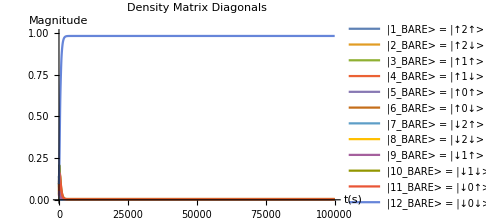
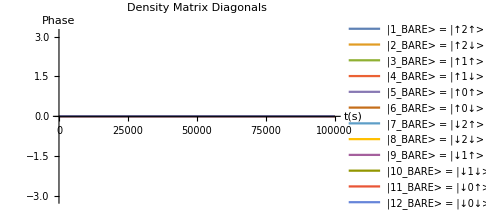

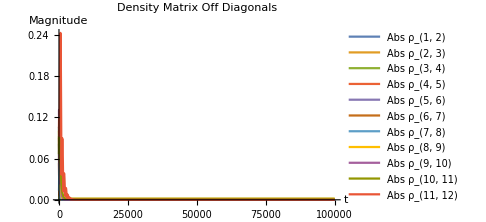
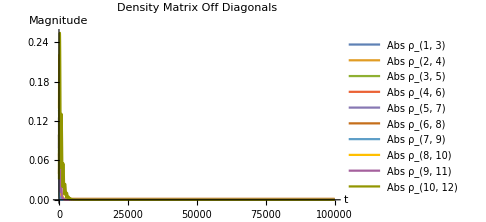
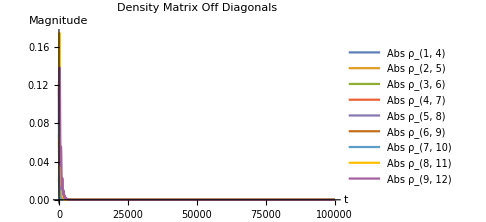

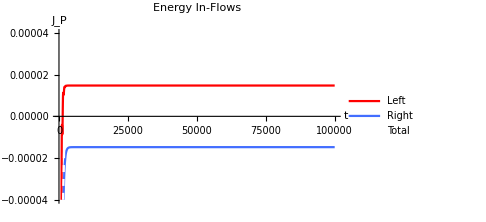

```mathematica
tmax=(50000/Subscript[ω, 2])//.Flatten[{unitassum,Tassum}];

dynamics=NDSolve[
Flatten[{sol//.Flatten[{γassum,NBEassum,unitassum,Tassum,Jassum}],Table[Subscript[ρ, i,j][0]==initρMatrix[[i,j]],{i,1,12},{j,1,12}]}]
,Flatten[Table[Subscript[ρ, i,j],{i,1,12},{j,1,12}]],{t,0,tmax}
];

plot1=Flatten[{Table[Abs[Subscript[ρ, i,i][t]],{i,1,12}]}/.dynamics];
plot2=Flatten[{Table[Arg[Subscript[ρ, i,i][t]],{i,1,12}]}/.dynamics];
{Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Density Matrix Diagonals"],
	PlotRange-> {0,1},
	AxesLabel->{Style["t(s)"],Style["Magnitude"]}, 
	PlotLegends->{
		Style["|1_BARE> = |↑2↑> "],Style["|2_BARE> = |↑2↓> "],
		Style["|3_BARE> = |↑1↑> "],Style["|4_BARE> = |↑1↓> "],
		Style["|5_BARE> = |↑0↑> "],Style["|6_BARE> = |↑0↓> "],
		Style["|7_BARE> = |↓2↑> "],Style["|8_BARE> = |↓2↓> "],
		Style["|9_BARE> = |↓1↑> "],Style["|10_BARE> = |↓1↓> "],
		Style["|11_BARE> = |↓0↑> "],Style["|12_BARE> = |↓0↓> "]
}],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Density Matrix Diagonals"],
	PlotRange-> {-π,π},
	AxesLabel->{Style["t(s)"],Style["Phase"]}, 
	PlotLegends->{
		Style["|1_BARE> = |↑2↑> "],Style["|2_BARE> = |↑2↓> "],
		Style["|3_BARE> = |↑1↑> "],Style["|4_BARE> = |↑1↓> "],
		Style["|5_BARE> = |↑0↑> "],Style["|6_BARE> = |↑0↓> "],
		Style["|7_BARE> = |↓2↑> "],Style["|8_BARE> = |↓2↓> "],
		Style["|9_BARE> = |↓1↑> "],Style["|10_BARE> = |↓1↓> "],
		Style["|11_BARE> = |↓0↑> "],Style["|12_BARE> = |↓0↓> "]
}]}

plot1=Flatten[{Abs[Subscript[ρ, 1,2][t]],Abs[Subscript[ρ, 2,3][t]],Abs[Subscript[ρ, 3,4][t]],Abs[Subscript[ρ, 4,5][t]],Abs[Subscript[ρ, 5,6][t]],Abs[Subscript[ρ, 6,7][t]],Abs[Subscript[ρ, 7,8][t]],Abs[Subscript[ρ, 8,9][t]],Abs[Subscript[ρ, 9,10][t]],Abs[Subscript[ρ, 10,11][t]],Abs[Subscript[ρ, 11,12][t]]}/.dynamics];
plot2=Flatten[{Abs[Subscript[ρ, 1,3][t]],Abs[Subscript[ρ, 2,4][t]],Abs[Subscript[ρ, 3,5][t]],Abs[Subscript[ρ, 4,6][t]],Abs[Subscript[ρ, 5,7][t]],Abs[Subscript[ρ, 6,8][t]],Abs[Subscript[ρ, 7,9][t]],Abs[Subscript[ρ, 8,10][t]],Abs[Subscript[ρ, 9,11][t]],Abs[Subscript[ρ, 10,12][t]]}/.dynamics];
plot3=Flatten[{Abs[Subscript[ρ, 1,4][t]],Abs[Subscript[ρ, 2,5][t]],Abs[Subscript[ρ, 3,6][t]],Abs[Subscript[ρ, 4,7][t]],Abs[Subscript[ρ, 5,8][t]],Abs[Subscript[ρ, 6,9][t]],Abs[Subscript[ρ, 7,10][t]],Abs[Subscript[ρ, 8,11][t]],Abs[Subscript[ρ, 9,12][t]]}/.dynamics];
{
Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Density Matrix Off Diagonals"],
	PlotRange-> Full,
	AxesLabel->{Style["t"],Style["Magnitude"]}, 
	PlotLegends->{
		Style["Abs ρ_(1, 2)"],Style["Abs ρ_(2, 3)"],
		Style["Abs ρ_(3, 4)"],Style["Abs ρ_(4, 5)"],
		Style["Abs ρ_(5, 6)"],Style["Abs ρ_(6, 7)"],
		Style["Abs ρ_(7, 8)"],Style["Abs ρ_(8, 9)"],
		Style["Abs ρ_(9, 10)"],Style["Abs ρ_(10, 11)"],
		Style["Abs ρ_(11, 12)"]}],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Density Matrix Off Diagonals"],
	PlotRange-> Full,
	AxesLabel->{Style["t"],Style["Magnitude"]}, 
	PlotLegends->{
		Style["Abs ρ_(1, 3)"],Style["Abs ρ_(2, 4)"],
		Style["Abs ρ_(3, 5)"],Style["Abs ρ_(4, 6)"],
		Style["Abs ρ_(5, 7)"],Style["Abs ρ_(6, 8)"],
		Style["Abs ρ_(7, 9)"],Style["Abs ρ_(8, 10)"],
		Style["Abs ρ_(9, 11)"],Style["Abs ρ_(10, 12)"]}],
Plot[plot3,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Density Matrix Off Diagonals"],
	PlotRange-> Full,
	AxesLabel->{Style["t"],Style["Magnitude"]}, 
	PlotLegends->{
		Style["Abs ρ_(1, 4)"],Style["Abs ρ_(2, 5)"],
		Style["Abs ρ_(3, 6)"],Style["Abs ρ_(4, 7)"],
		Style["Abs ρ_(5, 8)"],Style["Abs ρ_(6, 9)"],
		Style["Abs ρ_(7, 10)"],Style["Abs ρ_(8, 11)"],
		Style["Abs ρ_(9, 12)"]}]
}

Flatten[{Subscript[EngyFlowIn, 1][ρMatrix[t]],Subscript[EngyFlowIn, 2][ρMatrix[t]],Subscript[EngyFlowIn, 1][ρMatrix[t]]+Subscript[EngyFlowIn, 2][ρMatrix[t]]}//.Flatten[{γassum,NBEassum,unitassum,Tassum,Jassum}]/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Energy In-Flows"],
	PlotRange->{-0.00004,0.00004},
	AxesLabel->{"t","J_P"},
	PlotLegends->{"Left ","Right","Total"},
	PlotStyle->{Red,BlueC,{White,Dashed}}]
```

Dynamics of the complete density matrix,

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[ω, 1]->1.0 ωconv,Subscript[ω, 2]->0.5 ωconv,Subscript[ω, 3]->0.5ωconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01};
```

```mathematica
γassum={γLM->0.01ωconv,γMR->0.01ωconv};
```

```mathematica
tmax=(5000/Subscript[ω, 2])//.Flatten[{unitassum,Tassum}];

dynamics=NDSolve[
Flatten[{sol//.Flatten[{γassum,NBEassum,unitassum,Tassum,Jassum}],Table[Subscript[ρ, i,j][0]==initρMatrix[[i,j]],{i,1,12},{j,1,12}]}]
,Flatten[Table[Subscript[ρ, i,j],{i,1,12},{j,1,12}]],{t,0,tmax}
];

Manipulate[
temp=Abs[ArrayReshape[Table[Subscript[ρ, i,j][t],{i,1,12},{j,1,12}]/.dynamics,{12,12}]];
{ListPointPlot3D[Log[temp],PlotRange->{-15,1},ColorFunction->"TemperatureMap",ImageSize->Large],DecimalForm[MatrixForm[temp],{4,3}]}
,{{t,0},0,tmax}]
```

## Numerically obtaining the approximate steady-state

```mathematica
varFunc[T1_,T2_,κ1_,κ2_,ω1_,ω2_,ω3_,γLMs_,γMRs_,tmax_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{unitassum,NBEassum,Jassum,Subscript[T, 1]->T1,Subscript[T, 2]->T2,Subscript[κ, 1]->κ1,Subscript[κ, 2]->κ2,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,Subscript[ω, 3]->ω3,γLM->γLMs,γMR->γMRs}];
temp1=sol//.temp0;
temp2=NDSolve[
Flatten[{temp1,Table[Subscript[ρ, i,j][0]==i,j i,4 1,{i,1,12},{j,1,12}]}],Flatten[Table[Subscript[ρ, i,j],{i,1,12},{j,1,12}]],{t,0,tmax}];
temp3=Table[Subscript[ρ, i,j][tmax],{i,1,12},{j,1,12}]//.Flatten[temp2];
{
Re[Flatten[Table[Subscript[ρ, i,i][tmax],{i,1,12}]/.temp2]],
Re[Flatten[{Subscript[Τs, 2][1,2],Subscript[Τs, 1][1,3],Subscript[Τs, 1][2,4],Subscript[Τs, 2][3,4],Υs[2,3,tmax]}//.Flatten[{t->tmax,temp0}]/.temp2]],
Re[Flatten[{Subscript[EngyFlowIn, 1][ρMatrix[t]],Subscript[EngyFlowIn, 2][ρMatrix[t]]}//.Flatten[{t->tmax,temp0}]/.temp2]],
Table[Subscript[ρ, i,j][tmax],{i,1,12},{j,1,12}]//.temp2,
Re[Flatten[{Subscript[EngyFlowIn, 1][ρMatrix[t]],Subscript[EngyFlowIn, 2][ρMatrix[t]]}//.Flatten[{temp0}]/.temp2]]
}
]
```

```mathematica
varFunc[0.2,0.02,0.01,0.01,1.0,0.57,0.5,0.03,0.03,5000,unitassum];
```

## Energy flow characteristics for different system parameters

### Energy flow under different levels of resonance

Energy flows when ω_2 is changed from below ω_3 to above ω_3, keeping γs constant,

```mathematica
PlotEngyFlowsWithω2[T1_,T2_,κ1_,κ2_,ω1s_,ω2min_,ω2max_,ω3s_,γLMs_,γMRs_,tmax_,ωres_,legends_,title_]:=Module[{tempx,tempy,temp},
tempx=Table[{ω2,ω2},{ω2,ω2min,ω2max,ωres}];
tempy=10^5 Table[varFunc[T1,T2,κ1,κ2,ω1s,ω2,ω3s,γLMs,γMRs,tmax,unitassum],{ω2,ω2min,ω2max,ωres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,3,i]]}],{i,1,2}];
ListPlot[temp,
	PlotRange->{{ω2min,ω2max},{-4,4}},
	ImageSize->Medium,
	AxesStyle->Directive[Darker[Gray],13.5,FontFamily->"Times New Roman"],
	AxesLabel->{
		Style["ω_2",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_P(10^-5)",FontFamily->"Times New Roman",FontSize->14.5]},
	Joined->True,
  PlotLabel->Style[title,FontFamily->"Times New Roman",FontSize->14.5],
	PlotStyle->{{Red},{Blue}},
	PlotLegends->legends &&{
		Style["J_L",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_R",FontFamily->"Times New Roman",FontSize->14.5]}]
]
```

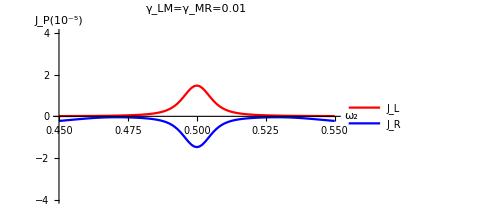
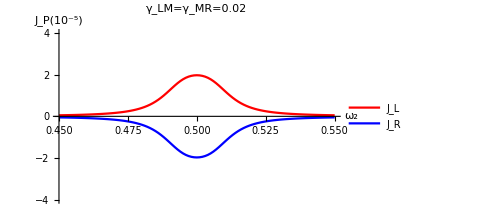
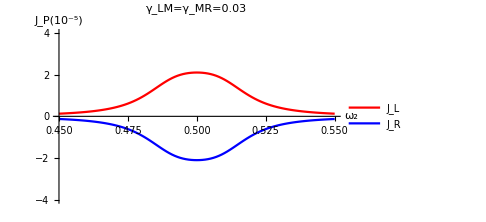

```mathematica
{
Module[{T1,T2,κ1,κ2,ω1,ω2min,ω2max,ω3,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs=0.01ωconv;
γMRs=0.01ωconv;
ω1=1.0ωconv;
ω2min=0.45ωconv;ω2max=0.55ωconv;ωres=0.001ωconv;
ω3=0.5ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ω2min,ω2max,ω3,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.01"]
],
Module[{T1,T2,κ1,κ2,ω1,ω2min,ω2max,ω3,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs=0.02ωconv;
γMRs=0.02ωconv;
ω1=1.0ωconv;
ω2min=0.45ωconv;ω2max=0.55ωconv;ωres=0.001ωconv;
ω3=0.5ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ω2min,ω2max,ω3,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.02"]
],
Module[{T1,T2,κ1,κ2,ω1,ω2min,ω2max,ω3,γLMs,γMRs,tmaxs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γLMs=0.03ωconv;
γMRs=0.03ωconv;
ω1=1.0ωconv;
ω2min=0.45ωconv;ω2max=0.55ωconv;ωres=0.001ωconv;
ω3=0.5ωconv;
tmaxs=50000/ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ω2min,ω2max,ω3,γLMs,γMRs,tmaxs,ωres,True,"γ_LM=γ_MR=0.03"]
]
}
```

### Energy flow under different levels of resonance and different coupling strengths

```mathematica
PlotEngyFlowsWithω2andγ[T1_,T2_,κ1_,κ2_,ω1s_,ω2min_,ω2max_,ω3s_,γmin_,γmax_,tmax_,ωres_,γres_,legends_]:=Module[{tempx,tempy,tempz,temp},
tempx=Table[ω2,{ω2,ω2min,ω2max,ωres},{γ,γmin,γmax,γres}];
tempy=Table[γ,{ω2,ω2min,ω2max,ωres},{γ,γmin,γmax,γres}];
tempz=10^5 Table[varFunc[T1,T2,κ1,κ2,ω1s,ω2,ω3s,γ,γ,tmax,unitassum][[3,1]],{ω2,ω2min,ω2max,ωres},{γ,γmin,γmax,γres}];
temp=MapThread[List,{Flatten[tempx][[;;]],Flatten[tempy][[;;]],Flatten[tempz][[;;]]}];
ListPlot3D[temp,
	PlotRange->{{ω2min,ω2max},{γmin,γmax},Full},
	ImageSize->Large,
	AxesStyle->Directive[Darker[Gray],13.5,FontFamily->"Times New Roman"],
	AxesLabel->{
		Style["ω_2",FontFamily->"Times New Roman",FontSize->14.5],
		Style["γ_LM=γ_MR",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_P(10^-5)",FontFamily->"Times New Roman",FontSize->14.5]},
	ColorFunction->"BlueGreenYellow"]
]
```

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ω2min,ω2max,ω3,γmin,γmax,tmaxs,ωres,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.00ωconv;γmax=0.03 ωconv;γres=0.0015;
ω1=1.0ωconv;
tmaxs=50000/ωconv;
ω2min=0.45ωconv;ω2max=0.55ωconv;ωres=0.001ωconv;
ω3=0.5ωconv;
PlotEngyFlowsWithω2andγ[T1,T2,κ1,κ2,ω1,ω2min,ω2max,ω3,γmin,γmax,tmaxs,ωres,γres,True]
]
```

-Graphics3D-